Here are the instructions for proper use of this program.
1.  Please don't touch Modules in Cells 0 through 11 (blue text at cell bottom
     are test statements that may be kept "as is"  or commented out).  
     Code is "ready to run" assuming download was OK.
2.  Execute Cells 0 through 11, in that order, to initialize all necessary modules. 
     Shortcut fo Mathematica 4 and 5: select Kernel -> Evaluation -> Evaluate Initialization.
     For Mathematica versions >=6, click Evaluate Initialization Cells.
3.  Cells 12A through 12D  contain test driver programs used to check the code.   
     It is recommended to run at least two (especially 12B, which is documented 
     in Addendum B of the exam) to verify that the downloaded NB works as expected.
4.  Cell 13 solves the Question 5 problem of the 2017 Final Exam with a very coarse mesh.  
     It may be used as a "template" for doing the finer mesh case in another cell, say Cell 14.
5.  If the plots produced by  running your driver program appear too small,  increase the
     value of imgsiz, which specifies the plot width in printer points (1 inch=72.27 points)
    If the plots look too big, reduce imgsiz.
6.  Plotting module news update. These are provided in 3 cells: 9A, 9B, 9C.
     o  Cell 9A: A new and spiffier mesh plotter, called Plot2DMesh, written Nov 2009.  
         Publication quality and fast but barely debugged and still undocumented.  
         Report any problems to instructor.
     o  Two contour plot modules are provided: 
         Cell 9B: polygon plotter ContourPlotNodeFuncOver2DMesh. - Old, reliable,
         but low quality and slow. Nsub=8 or 12  usually gives acceptable results for
         coarse meshes whereas Nsub=4  should be OK for finer meshes.
         Cell 9C: band plotter ContourBandPlotNodeFuncOver2DMesh. New, 
         fast and publication quality but barely debugged and still undocumented. 
         Report any problems to instructor.
7. To move a plot to a document: select cell that holds plot by clicking on margin, then
     Edit -> Save Selection As ->  Encapsulated PostScript (eps) and give file a name. 
     (Note: this is the sequence used in Mathematica 4.1-5.2, has changed in versions >=6.0)
     Quit Mathematica, pick file with Adobe Illustrator (or equivalent) to clean it up as 
     needed, and include in exam document.  To include in a Word document, convert to 
     a Microsoft  accepted format, such as jpeg, first.

Cell 0.   Global variables dependent on Mathematica version

```mathematica
DisplayChannel=$DisplayFunction;
If [$VersionNumber>=6.0, DisplayChannel=Print]; 
  (* fix for Mathematica 6 & later *)
```

```mathematica
Off[General::spell1]; Off[General::spell];
```

Cell 1.  Shape Functions of 4-Node Bilinear Quadrilateral.  This is the same module used
in structural problems and described in Chapter 17. To test code, uncomment blue text, run cell.

```mathematica
Quad4IsoPShapeFunDer[ncoor_,qcoor_]:= Module[
  {Nf,dNx,dNy,dNξ,dNη,i,J11,J12,J21,J22,Jdet,ξ,η,x,y},
  {ξ,η}=qcoor; 
   Nf={(1-ξ)*(1-η),(1+ξ)*(1-η),(1+ξ)*(1+η),(1-ξ)*(1+η)}/4;
   dNξ ={-(1-η), (1-η),(1+η),-(1+η)}/4;
   dNη= {-(1-ξ),-(1+ξ),(1+ξ), (1-ξ)}/4;
   x=Table[ncoor[[i,1]],{i,4}]; y=Table[ncoor[[i,2]],{i,4}];
   J11=dNξ.x; J21=dNξ.y; J12=dNη.x; J22=dNη.y;
   Jdet=Simplify[J11*J22-J12*J21];
   dNx= ( J22*dNξ-J21*dNη)/Jdet;  dNx=Simplify[dNx];
   dNy= (-J12*dNξ+J11*dNη)/Jdet;  dNy=Simplify[dNy];
   Return[{Nf,dNx,dNy,Jdet}]
];

(*ClearAll[a,b,ξ,η];
ncoor={{0,0},{a,0},{a,b},{0,b}};
{Nf,Nx,Ny,Jdet}=Simplify[Quad4IsoPShapeFunDer[ncoor,{ξ,η}]];
Print[{Nf,Nx,Ny,Jdet}];*)
```

Cell 2.  Gauss quadrature rule information for quadrilaterals.  This is the same module used
in  structural problems and described in Chapter 17. To test code, uncomment blue text, run cell.

```mathematica
QuadGaussRuleInfo[{rule_,numer_},point_]:= Module[
 {xi,eta,p1,p2,i1,i2,w1,w2,k,info=Null},
  If [Length[rule]==2,  {p1,p2}=rule, p1=p2=rule];
  If [Length[point]==2, {i1,i2}=point, 
      k=point; i2=Floor[(k-1)/p1]+1; i1=k-p1*(i2-1) ];
  {xi, w1}=  LineGaussRuleInfo[{p1,numer},i1];
  {eta,w2}=  LineGaussRuleInfo[{p2,numer},i2];
  info={{xi,eta},w1*w2};
  If [numer, Return[N[info]], Return[Simplify[info]]];
];
LineGaussRuleInfo[{rule_,numer_},point_]:= Module[
  {g2={-1,1}/Sqrt[3],w3={5/9,8/9,5/9}, 
   g3={-Sqrt[3/5],0,Sqrt[3/5]}, 
   w4={(1/2)-Sqrt[5/6]/6, (1/2)+Sqrt[5/6]/6,
       (1/2)+Sqrt[5/6]/6, (1/2)-Sqrt[5/6]/6},
   g4={-Sqrt[(3+2*Sqrt[6/5])/7],-Sqrt[(3-2*Sqrt[6/5])/7],
        Sqrt[(3-2*Sqrt[6/5])/7], Sqrt[(3+2*Sqrt[6/5])/7]},
   g5={-Sqrt[5+2*Sqrt[10/7]],-Sqrt[5-2*Sqrt[10/7]],0, 
        Sqrt[5-2*Sqrt[10/7]], Sqrt[5+2*Sqrt[10/7]]}/3,
   w5={322-13*Sqrt[70],322+13*Sqrt[70],512,
       322+13*Sqrt[70],322-13*Sqrt[70]}/900,
   i=point,p=rule,info={Null,0}}, 
  If [p==1, info={0,2}];
  If [p==2, info={g2[[i]],1}];
  If [p==3, info={g3[[i]],w3[[i]]}]; 
  If [p==4, info={g4[[i]],w4[[i]]}];
  If [p==5, info={g5[[i]],w5[[i]]}];
  If [numer, Return[N[info]], Return[Simplify[info]]];
];
```

Cell 3.   Formation of "element stiffness" matrix of 4-node quad for Poisson's equation.    
Can be used for many problems: potential fluid flow, electrostatics, torsion, etc,  
including the  steady-state heat conduction problem of the 2009 Final Exam.  
Relevant to part of Question 2 of that exam. To test code, uncomment blue text, run cell.

```mathematica
Quad4IsoPPoissonStiffness[ncoor_,mprop_,fprop_,opt_]:= 
  Module[{i,k,l,p=2,num=False,Emat,th=1,h,qcoor,w,
         kcond, Nf,Nx,Ny,Jdet,Be,Ke=Table[0,{4},{4}]},
  If [Length[fprop]>0, th=fprop[[1]]];
  If [Length[mprop]>0, kcond=mprop[[1]], kcond=mprop];  
  If [Length[opt]>0,   num=opt[[1]]];
  If [Length[opt]>1,   p  =opt[[2]]];
  If [p<1||p>4, Print["p out of range"]; Return[Null]];
  For [k=1, k<=p, k++,  
    For [l=1, l<=p, l++, 
        {qcoor,w}=        QuadGaussRuleInfo[{p,num},{k,l}];
        {Nf,Nx,Ny,Jdet}=  Quad4IsoPShapeFunDer[ncoor,qcoor];
        If [num, {Nf,Nx,Ny,Jdet}=N[{Nf,Nx,Ny,Jdet}]];
        If [Length[th]==0, h=th, h=th.Nf]; Be={Nx,Ny}; 
        Ke +=w*Jdet*kcond*h*(Transpose[Be].Be);     
        ]; 
      ]; Return[Simplify[Ke]]
   ];
   
ClearAll[a,b,k,h];  h=1;  k=6;
Ke=Quad4IsoPPoissonStiffness[{{0,0},{a,0},{a,b},{0,b}},
  k,{h},{False,2}]; (* rectangle, symbolic eval, 2x2 Gauss rule  *)
Print["Ke=",Ke//MatrixForm]; Print["eigs of Ke=",Eigenvalues[Ke]];
(*Ke=Quad4IsoPPoissonStiffness[{{0,0},{a,0},{a,b},{0,b}},
  k,{h},{False,1}]; (* rectangle, symbolic eval, 1x1 Gauss rule  *)
Print["Ke=",Ke//MatrixForm]; Print["eigs of Ke=",Eigenvalues[Ke]];*)
```

Ke=((2 a)/b+(2 b)/a | a/b-(2 b)/a | -a/b-b/a | -(2 a)/b+b/a
a/b-(2 b)/a | (2 a)/b+(2 b)/a | -(2 a)/b+b/a | -a/b-b/a
-a/b-b/a | -(2 a)/b+b/a | (2 a)/b+(2 b)/a | a/b-(2 b)/a
-(2 a)/b+b/a | -a/b-b/a | a/b-(2 b)/a | (2 a)/b+(2 b)/a)

eigs of Ke={0,(6 a)/b,(6 b)/a,(2 (a^2+b^2))/(a b)}

Cell 4.   Computes consistent  node forces fe due to body source (called s) within 
element.  This is constant over element if specified as a scalar s, or varies 
bilinearly if given as {s1,s2,s3,s4}.  For the heat conduction problem, this source is the 
heat production (if +)  or comsumption (if -) per body volume.   Relevant to part of
Question 3 of the 2009 Final Exam. To test code, uncomment blue text, run cell.

```mathematica
Quad4IsoPPoissonSourceForces[ncoor_,mprop_,fprop_,forprop_,
   opt_]:= Module[{i,k,l,p=2,num=False,Emat,th=1,h,qcoor,c,w,
   s=0,source,Nx,Ny,Jdet,fe=Table[0,{4}]},
  If [Length[fprop]>0, th=fprop[[1]]];
  If [Length[forprop]>0, s=forprop[[1]], Return[fe] ]; 
  If [Length[opt]>0, num=opt[[1]]];
  If [Length[opt]>1, p  =opt[[2]]];
  If [p<1||p>4, Print["p out of range"];Return[Null]];
  For [k=1, k<=p, k++, 
    For [l=1, l<=p, l++, 
        {qcoor,w}=        QuadGaussRuleInfo[{p,num},{k,l}];
        {Nf,Nx,Ny,Jdet}=  Quad4IsoPShapeFunDer[ncoor,qcoor];
         If [num, {Nf,Nx,Ny,Jdet}=N[{Nf,Nx,Ny,Jdet}]];
         If [Length[th]==0, h=th, h=th.Nf]; c=w*Jdet*h;
         If [Length[s ]==0, source=s, source=s.Nf]; 
         fe+=w*Jdet*source*h*Nf;     
        ]; 
      ]; Return[Simplify[fe]]
   ];
   
ClearAll[a,b,k,h,s,s1,s2,s3,s4];  
ncoor={{0,0},{a,0},{a,b},{0,b}};
fe=Quad4IsoPPoissonSourceForces[ncoor,{k},{h},{s},{False,2}];
Print["Constant source node forces fe=",fe];
fe=Quad4IsoPPoissonSourceForces[ncoor,{k},{h},{{s1,s2,s3,s4}},
    {False,2}];
(*Print["Varying source node forces fe=",fe];*)
```

Constant source node forces fe={1/4 a b h s,1/4 a b h s,1/4 a b h s,1/4 a b h s}

Cell 5.   Computes consistent  node forces fe due to specified normal flux qn over element sides.
This is entered as  q={q12,q23,q34,q41} in the second entry of forprop.   Fluxes are assumed 
constant over each side.   A flux is positive it it flows away from element, that is, along its exterior normal.
If the flux over a side is unknown (e.g. internal side) enter zero.  Trailing zeros may be omitted, for 
example qn={0,q23} means flux is known only over  side 2-3. If all fluxes are unknown, an empty list 
may be given, or the entry left out from forprop.  For the heat conduction problem, fluxes are the 
thermal fluxes conducting energy away or into elements.  A positive thermal flux, say q12, means that 
element is losing heat at the rate q12 along side 1-2.  Relevant to Question 4 of 2009 Final Exam.
To test code, uncomment blue text, run cell.

```mathematica
Quad4IsoPPoissonFluxForces[ncoor_,mprop_,fprop_,forprop_,
   opt_]:= Module[{i,j,num=False,th=1,q, h,hm,
      xi,xj,yi,yj,L, fe=Table[0,{4}]},
  If [Length[fprop]>0, th=fprop[[1]]];
  If [Length[th]==0, h={th,th,th,th}, h=th]; 
  If [Length[forprop]>1, q=forprop[[2]], Return[fe]];
  If [Length[opt]>0, num=opt[[1]]];
  For [i=1, i<=Length[q], i++, If [i<4, j=i+1, j=1];  
       {xi,yi}=ncoor[[i]]; {xj,yj}=ncoor[[j]];
       L=PowerExpand[Sqrt[(xj-xi)^2+(yj-yi)^2]]; 
       hm=(h[[i]]+h[[j]])/2;
       fe[[i]]-=hm*q[[i]]*L/2; fe[[j]]-=hm*q[[i]]*L/2;       
      ]; Return[Simplify[fe]]
   ];

ClearAll[a,b,k,h,h1,h2,h3,h4,q12,q23,q34,q41];
ncoor={{0,0},{a,0},{a,b},{0,b}};
fe=Quad4IsoPPoissonFluxForces[ncoor,{k},{h},
  {0,{q12,0,0,0}},{False}];
Print["Flux over 4 sides, const h, fe=",fe];
(*fe=Quad4IsoPPoissonFluxForces[ncoor,{k},{h},{0,{0,q23}},{False}];
Print["Flux over 2-3, const h, fe=",fe];*)
```

Flux over 4 sides, const h, fe={-1/2 a h q12,-1/2 a h q12,0,0}

Cell 6.  Assembly of master stiffness of Poisson problem as a full symmetric matrix.  This module
is similar to the assemblers for structural problems, with the simplification that there is only one
DOF per node.  Hence the element nodelist (enl) and the element freedom table (eftab) coalesce.
To test code, uncomment blue text, run cell.

```mathematica
MasterStiffnessPoisson[nodcoor_,eletyp_,elenod_,elemat_,
  elefab_,eleopt_]:=Module[
  {numele=Length[elenod],numnod=Length[nodcoor],neldof,e,enl,
  eftab,n1,n2,n3,n4,i,j,ncoor,mprop,fprop,opt,Ke,K},
  K=Table[0,{numnod},{numnod}];
  For [e=1, e<=numele, e++,
     enl=elenod[[e]]; eftab={n1,n2,n3,n4}=enl; 
     ncoor={nodcoor[[n1]],nodcoor[[n2]],
            nodcoor[[n3]],nodcoor[[n4]]};           
     mprop=elemat[[e]]; fprop=elefab[[e]]; opt=eleopt;  
     Ke=Quad4IsoPPoissonStiffness[ncoor,mprop,fprop,opt];
     neldof=Length[Ke];
     For [i=1, i<=neldof, i++, ii=eftab[[i]];
         For [j=i, j<=neldof, j++, jj=eftab[[j]];
             K[[jj,ii]]=K[[ii,jj]]+=Ke[[i,j]] 
         ];
       ];
     ];
  Return[K]
  ];

(*eletyp=Table["Quad4",{2}]; (* eletyp is dummy placeholder *)
nodcoor={{0,1},{0,0},{2,1},{2,0},{4,1},{4,0}};
elenod={{1,2,4,3},{3,4,6,5}}; elemat={12,12}; elefab={1,1};     
K=MasterStiffnessPoisson[nodcoor,eletyp,elenod,elemat,elefab,{True} ];
Print["Master stiffness of Poisson FEM model:"]; 
Print[K//MatrixForm];
Print ["eigs of K=",Chop[Eigenvalues[K]]];*)
```

Cell 7.  Assembles the master node force vector of a Poisson  FEM model.   This assembler goes 
element by element.  It gets consistent node forces dues to sources and fluxes from the
force modules in Cells 4 and 5,  and merges those into the master force vector.
To test code, uncomment blue text, run cell.

```mathematica
MasterNodeForcesPoisson[nodcoor_,eletyp_,elenod_,elemat_,
   elefab_,elefor_,eleopt_]:=Module[
  {numele=Length[elenod],numnod=Length[nodcoor],neldof,e,eNL,
  eftab,n1,n2,n3,n4,i,j,ncoor,mprop,fprop,forprop,opt,fe,f},
  f=Table[0,{numnod}];
  For [e=1, e<=numele, e++,
     eNL=elenod[[e]]; eftab={n1,n2,n3,n4}=eNL; 
     ncoor={nodcoor[[n1]],nodcoor[[n2]],
            nodcoor[[n3]],nodcoor[[n4]]};           
     mprop=  elemat[[e]]; fprop=elefab[[e]]; 
     forprop=elefor[[e]]; opt=eleopt;  
     fe=Quad4IsoPPoissonSourceForces[ncoor,mprop,fprop,
          forprop,opt]+
        Quad4IsoPPoissonFluxForces  [ncoor,mprop,fprop,
          forprop,opt];
     neldof=Length[fe];
     For [i=1, i<=neldof, i++, ii=eftab[[i]]; f[[ii]]+=fe[[i]] 
         ];
     ];
  Return[f]
  ];
  
(*ClearAll[s1,s2,q12,q24,q65];
eletyp=Table["Quad4",{2}]; (* eletyp is dummy placeholder *)
nodcoor={{0,4},{0,0},{3,4},{3,0},{4,4},{4,0}};
elenod={{1,2,4,3},{3,4,6,5}}; elemat={12,12}; elefab={1,1};
elefor={{s1},{s2}};     
f=MasterNodeForcesPoisson[nodcoor,eletyp,elenod,
         elemat,elefab,elefor,{False} ];
Print["Master forces of Poisson model:"]; Print[f];
elefor={{0,{q12,q24,0,0}},{0,{0,0,q65,0}}};     
f=MasterNodeForcesPoisson[nodcoor,elenod,
         elemat,elefab,elefor,{False} ];
Print["Master forces of Poisson model:"]; Print[f];*)
```

Cell 8.  Application of prescribed-dof boundary conditions.  These modules are similar to those 
presented for structural problems, except that ModifiedNodeForces accounts for prescribed
nonzero node values.  This is important for the heat conduction problem because prescribed
nodal temperatures are generally nonzero. To test code, uncomment blue text, run cell.

```mathematica
ModifiedMasterStiffness[pdof_,K_]:= Module[
   {i,j,k,Kii,Kmod=K}, 
    For [k=1, k<=Length[pdof], k++, i=pdof[[k]]; Kii=1;
        For [j=1, j<=Length[K], j++, 
            Kmod[[i,j]]=Kmod[[j,i]]=0]; Kmod[[i,i]]=Kii;
        ]; Return[Kmod]
];
ModifiedNodeForces[pdof_,d_,K_,f_]:= Module[
  {i,j,k,l,m=Length[pdof],n=Length[K],fixed,fmod=f}, 
    fixed=Table[False,{n}]; 
    For [k=1, k<=m, k++, i=pdof[[k]]; fixed[[i]]=True];
    For [k=1, k<=m, k++, i=pdof[[k]]; 
        For [j=1, j<=n, j++, If [fixed[[j]],Continue[]];  
             fmod[[j]]-=K[[i,j]]*d[[k]]; 
            ]; fmod[[i]]=d[[k]]; 
        ]; 
    Return[fmod];
];
  
(* ClearAll[Ks,fs,d1,d2,d3];    
K=Array[Ks,{6,6}];
Print["Master stiffness matrix:"]; Print[K//MatrixForm];
f=Array[fs,{6}];
Print["Master node force vector:"]; Print[f];
f=ModifiedNodeForces[{1,2,4},{d1,d2,d3},K,f];
Print["Node force vector modified for displacement B.C.:"];
Print[f];
K=ModifiedMasterStiffness[{1,2,4},K];
Print["Stiffness matrix modified for displacement B.C.:"];
Print[K//MatrixForm]; *)
```

Cell 9A:  New mesh plotter Plot2DMesh, written Novembr 2009. Fancier, faster and
higher quality than the old one but less exhautively tried. To test code, uncomment blue text, run cell.

```mathematica
Plot2DMesh[nodxyz_,eletyp_,elenod_,eleplt_,typdat_,
   nodpar_,elepar_,{drawframe_,drawnodes_,nodfill_,
   labelem_,labnodes_},aspect_,imgsiz_,title_]:=Module[
 {i,j,k,n,m,numele=Length[elenod],numnod=Length[nodxyz],
  eletag,numobj,nodtag,ktypes,typtag,typhue,type,tk,e,enl,
  nen,etab,kelems,ke,pefill,pesid,pelab,pecirc,pedisk,
  epar=Length[elepar],npar=Length[nodpar],
  ecirad,ecirth,eshrink,efntsiz,efillhue,estyle,
  ncirad,ncirth,nlabofx,nlabofy,fntsiz,nfillhue,h,b,s,
  nstyle,knodes,pncirc,pnfill,pnlab,shrink,erad,
  idim,enlb,exy,exys,exybs,exy0,msg,nbn,n1,n2,nside,
  eginfo,nodcon,ncon,omitnodes=!drawnodes}, i=0;
  eletag=Table[1,{numele}]; numobj=Length[eleplt];  
  If [numobj>0,eletag=Plot2DTagObjects[numele,eleplt]];
  (*Print["eletag=",eletag]; *) 
  {ecirad,ecirth,eshrink,efntsiz,efillhue}=
      {8,1.5,1,12,{0.15,1,1}}; 
  If [epar==1,{ecirad}=elepar];    
  If [epar==2,{ecirad,ecirth}=elepar];  
  If [epar==3,{ecirad,ecirth,eshrink}=elepar];   
  If [epar==4,{ecirad,ecirth,eshrink,efntsiz}=elepar];  
  If [epar==5,{ecirad,ecirth,eshrink,efntsiz,efillhue}=elepar];
  (*Print["ecirad,ecirth,eshrink,efntsiz,efillhue=",
        {ecirad,ecirth,eshrink,efntsiz,efillhue}];*)
  shrink=!(eshrink==1||eshrink==1.0); 
  estyle=TextStyle->{FontFamily->"Times",FontSize->efntsiz,
         FontWeight->"Plain",FontSlant->"Plain"};
  ktypes=Length[typdat]; typtag={"All"}; typhue={efillhue};
  If [ktypes>0, typtag=Table[" ",{ktypes}];
      typhue=Table[efillhue,{ktypes}];
      (*Print["initial typtag=",typtag,"\ninitial typhue=",typhue];*)
      For [k=1,k<=ktypes,k++, tk=typdat[[k]]; 
           If [Length[tk]==0,typtag[[k]]=tk];
           If [Length[tk]>=1,typtag[[k]]=tk[[1]]];
           If [Length[tk]>=2,typhue[[k]]=tk[[2]]]];
      For [e=1,e<=numele,e++,
           etag=eletag[[e]]; If [etag==0,Continue[]];       
           If[!MemberQ[typtag,eletyp[[e]]],eletag[[e]]=0];
           ];
     ];
  (*Print["typtag and hue=",{typtag,typhue}//MatrixForm];
  Print["eletag after typtag=",eletag];*)
  kelems=Sum[eletag[[i]],{i,numele}]; 
  If [kelems<=0, Print["Plot2DMesh: empty plot"]; Return[]]; 
  pefill=peside=pecirc=pedisk=pelab=Table[{},{kelems}];  
  If [!labelems,pefill=pecirc=pelab={}];
  nodtag=Table[0,{numnod}];
  For [e=1,e<=numele,e++, If [eletag[[e]]==0,Continue[]];
     enl=elenod[[e]];        
     For [i=1,i<=Length[enl],i++, n=enl[[i]]; 
          If [shrink,nodtag[[n]]+=1,nodtag[[n]]=1]];
          ];
  knodes=Sum[nodtag[[i]],{i,numnod}];
  (*Print["knodes=",knodes];*)
  If [knodes>0,pncirc=pnfill=pnlab=Table[{},{knodes}]];  
  If [omitnodes,pncirc=pnfill=pnlab={}];  
  If [!labnodes,pnlab={}];
      {ncirad,ncirth,nlabofx,nlabofy,nfntsiz,nfillhue}=
      {3,1.5,-8,5,12,{0.7,0.2,0.9}};
 (*Print["ncirad,ncirth,nlabofx,nlabofy,nfntsiz,nfillhue=",
        {ncirad,ncirth,nlabofx,nlabofy,nfntsiz,nfillhue}];*)
  If [npar==1,{ncirad}=nodpar];    
  If [npar==2,{ncirad,ncirth}=nodpar];  
  If [npar==3,{ncirad,ncirth,nlabofx}=nodpar];   
  If [npar==4,{ncirad,ncirth,nlabofx,nlabofy}=nodpar];  
  If [npar==5,{ncirad,ncirth,nlabofx,nlabofy,nfntsiz}=nodpar];  
  If [npar==6,{ncirad,ncirth,nlabofx,nlabofy,nfntsiz,nfillhue}=nodpar];
  nstyle=TextStyle->{FontFamily->"Times",FontSize->nfntsiz,
                     FontWeight->"Plain",FontSlant->"Plain"};
  {h,s,b}=nfillhue; nodcon=Table[{},{numnod}];  
  lastyp="All";  k=0;
  For [e=1,e<=numele,e++, If [eletag[[e]]==0,Continue[]]; k++;
       type=eletyp[[e]]; enl=elenod[[e]]; nen=Lenghth[enl]; 
      {idim,enlb,exy,exys,exybs,exy0,msg}=Plot2DElemGeoInfo[
       type,nodxyz,enl,eshrink];
       (*Print["idim,enlb,exys,exybs,exy0=",
        {idim,enlb,exys,exybs,exy0}," msg=",msg]; *)
       If [msg!=" ", Print["Plot2DMesh: ",msg,", at elem ",e,
           "  Plot skipped"]; Return[]]; nbn=Length[enlb];
       eginfo={idim,enlb,exy,exys,exybs,exy0,ecirad,
               labelem,estyle,shrink};      
      {gefill,geside,gedisk,gecirc,gelab}=Plot2DIndElement[
              e,type,eginfo,nodcon];
       If [lastyp!=type, kk=Position[typtag,type]; 
           (*Print["lastyp,=",lastyp," type=",type," kk=",kk];*)
           If [kk=={}, kt=0; {h,s,b}=efillhue, 
                      {{kt}}=kk; {h,s,b}=typhue[[kt]]];
           gefill={Graphics[Hue[h,s,b]],gefill};
           lastyp=type];
      {pefill[[k]],peside[[k]],pedisk[[k]],pecirc[[k]],
       pelab[[k]]}={gefill,geside,gedisk,gecirc,gelab};       
       If [!shrink,
           For [i=1,i<=nbn,i++, j=i+1; If [i==nbn,j=1];
                nside={enlb[[i]],enlb[[j]]};               
                n1=Min[nside]; n2=Max[nside]; ncon=nodcon[[n1]];               
                If [MemberQ[ncon,n2], Continue[]];
                AppendTo[ncon,n2]; nodcon[[n1]]=Sort[ncon]]; 
           ];
      ];  (*Print["final nodcon=",nodcon]; *)
      
   If [drawnodes,      
      If [!shrink,
          {pncirc,pnfill,pnlab}=Plot2DNonShrunkNodes[nodxyz,nodtag,
          {ncirad,ncirth,nlabofx,nlabofy,nfntsiz},{nodfill,labnodes}];
         ];      
      If [shrink,
          {pncirc,pnfill,pnlab,msg}=Plot2DShrunkNodes[
          nodxyz,nodtag,{ncirad,ncirth,nlabofx,nlabofy,nfntsiz},
          {nodfill,labnodes},eletyp,elenod,eletag,eshrink];
          If [msg!=" ",Return[]]
         ];         
     ];   
  {h,s,b}=efillhue;          
  Show[Graphics[Hue[h,s,b]],pefill,
       Graphics[Hue[0,0,0]],Graphics[AbsoluteThickness[1.5]],
       peside,Graphics[GrayLevel[1]],pedisk,
       Graphics[GrayLevel[0]],pecirc,pelab,
       Graphics[RGBColor[0,0,0]],
       Graphics[AbsoluteThickness[1.5]],
       Graphics[GrayLevel[.7]],
       pnfill,Graphics[GrayLevel[0]],pncirc,pnlab,
       PlotRegion->{{0,1},{0,1}},
       Background->GrayLevel[.95],
       PlotLabel->title,AspectRatio->aspect,Frame->drawframe,
       ImageSize->imgsiz,DisplayFunction->DisplayChannel ];
   ClearAll[eletag,nodtag,nodcon,pefill,pesid,
        pncirc,pedisk,pnlab];
];

Plot2DTagObjects[numobj_,objplt_]:=Module[{i,j,
  k,l,m,n,obj,h,objtag=Table[0,{numobj}]},
  For [m=1,m<=Length[objplt],m++, 
       obj=objplt[[m]]; l=Length[obj]; h=Head[obj];
       If [h==Integer, n=obj; 
          If [n>0&&n<=numobj, objtag[[n]]=1]];
       If [h==List&&l==1, {n}=obj; 
          If [n>0&&n<=numobj, objtag[[n]]=1]];
       If [h==List&&l==2, {i,j}=obj; 
          For [n=Min[i,j],n<=Max[i,j],n++, 
          If [n>0&&n<=numobj, objtag[[n]]=1]]];
       If [h==List&&l==3, {i,j,k}=obj; k=Abs[k]; 
          For [n=Min[i,j],n<=Max[i,j],n+=k, 
          If [n>0&&n<=numobj, objtag[[n]]=1]]];
       ]; Return[objtag]];
       
          
Plot2DElemGeoInfo[type_,nodxyz_,enl_,eshrink_]:=Module[
  {i,k,kp,m1,m2,typedot=type<>".",name,idim=0,bn,nbn,
   enamtab={"Bar2",  1,2,{1,2},
            "Bar3",  1,3,{1,3,2}, 
            "Trig3", 2,3,{1,2,3},
            "Trig4", 2,4,{1,4,2,3},  
            "Trig5", 2,5,{1,4,2,6,3}, 
            "Trig6", 2,6,{1,4,2,5,3,6},
            "Trig9", 2,9,{1,4,5,2,6,7,3,8,9},
            "Trig10",2,10,{1,4,5,2,6,7,3,8,9},
            "Quad4", 2,4,{1,2,3,4}, 
            "Quad8", 2,8,{1,5,2,6,3,7,4,8},
            "Quad9", 2,9,{1,5,2,6,3,7,4,8},
            "Quad12",2,12,{1,5,6,2,7,8,3,9,10,4,11,12},
            "Quad16",2,16,{1,5,6,2,7,8,3,9,10,4,11,12}},
   nen,nenl,enlb,exy,exys,exyb,exybs,exy0,exy0s}, 
   enlb=exyb=exybs=exy0={}; 
   {{m1,m2}}=StringPosition[typedot,".",1]; 
   name=StringTake[type,m1-1]; k=Position[enamtab,name]; 
   If [k=={},kp=0,{{kp}}=k]; 
   If [kp==0, Return[{0,0,0,0,0,0,"Illegal elem type "<>type}]];
   {idim,nen,bn}=Take[enamtab,{kp+1,kp+3}]; nbn=Length[bn];
   (*Print["type=",type," k=",k," idim,nen,bn=",{idim,nen,bn}];*)
   nbn=Length[bn]; nenl=Length[enl]; 
   If [nbn<=0, Return[{0,0,0,0,0,0,"No boundary nodes"}]];
   If [nen!=neln, Return[{0,0,0,0,0,0,"Incorrect nodelist"}]];
   enlb=Table[enl[[bn[[i]]]],{i,nbn}];
   exy =Table[Take[nodxyz[[enl[[i]]]],2],{i,nen}]; 
   exyb=Table[exy[[bn[[i]]]],{i,nbn}];
   exy0=Sum[exyb[[i]],{i,nbn}]/nbn;
   If [eshrink==1||eshrink==1.0,
       Return[{idim,enlb,exy,exy,exyb,exy0," "}]];
   exy0s=(1-eshrink)*exy0;
   exys= Table[exy0s+eshrink*exy [[i]],{i,nen}];
   exybs=Table[exys[[bn[[i]]]],{i,nbn}];
   Return[{idim,enlb,exy,exys,exybs,exy0," "}]];
   
       
Plot2DNonShrunkNodes[nodxyz_,nodtag_,npars_,nflags_]:=
   Module[{n,k=0,numnod=Length[nodxyz],
   ncirad,ncirth,nlabofx,nlabofy,nfntsiz,
   nodfill,labnodes,knodes,x,y,
   xytext,rnod,nlab,style,pncirc,pnfill,pnlab},
  {ncirad,ncirth,nlabofx,nlabofy,nfntsiz}=npars;
  {nodfill,labnodes}=nflags;
   knodes=Sum[nodtag[[i]],{i,numnod}];
   pncirc=pnfill=pnlab=Table[{},{knodes}]; 
   If [!nodfill,pnfill={}]; If [!labnodes,pnlab={}];
   style=TextStyle->{FontFamily->"Times",FontSize->nfntsiz,
                     FontWeight->"Plain",FontSlant->"Plain"};  
   For [n=1,n<=numnod,n++, If [nodtag[[n]]==0, Continue[]]; 
       k++; {x,y}=Take[nodxyz[[n]],2];
       rnod=  Offset[N[{ncirad,ncirad}]];
       pncirc[[k]]= Graphics[Circle[{x,y},rnod]];
       If [nodfill, pnfill[[k]]=Graphics[Disk[{x,y},rnod]]];
       If [labnodes, nlab=ToString[n]; 
           xytext=Offset[N[{nlabofx,nlabofy}],{x,y}];
           pnlab[[k]]=Graphics[Text[nlab,xytext,style]]];
      ];
   Return[{pncirc,pnfill,pnlab}]];

Plot2DShrunkNodes[nodxyz_,nodtag_,npars_,nflags_,
   eletyp_,elenod_,eletag_,eshrink_]:=Module[{e,n,i,
   numnod=Length[nodxyz],numele=Length[elenod],k=0,klab=0,
   ncirad,ncirth,nlabofx,nlabofy,nfntsiz,nodfill,labnodes,
   knodes,knlabs,labtag,type,enl,nen,enlb,exyb,exy0,x,y,
   xs,ys,exy,exys,xytext,rnod,nlab,style,pncirc,pnfill,pnlab},
  {ncirad,ncirth,nlabofx,nlabofy,nfntsiz}=npars;
  {nodfill,labnodes}=nflags; 
   If [labnodes, worig=4;
       nlabxy=worig*nodxyz; nlabct=Table[worig,{numnod}];
       For [e=1,e<=numele,e++, If [eletag[[e]]==0,Continue[]];
           enl=elenod[[e]]; nen=Length[enl]; type=eletyp[[e]];
          {idim,enlb,exy,exys,exybs,exy0,msg}=Plot2DElemGeoInfo[
          type,nodxyz,enl,eshrink]; If [msg!=" ",Continue[]];
           For [i=1,i<=nen,i++, n=enl[[i]];
                nlabxy[[n]]+=exys[[i]]; nlabct[[n]]+=1] ];
      ]; 
   (* For [n=1,n<=numnod,n++,nlabxy[[n]]/=nlabct[[n]]];*)
   (* Print["nlabxy=",nlabxy]; Print["nlabct=",nlabct];*)
   knodes=Sum[nodtag[[i]],{i,numnod}];
   knlabs=Sum[Min[nodtag[[i]],1],{i,numnod}];
   labtag=Table[1,{numnod}];
   pncirc=pnfill=Table[{},{knodes}]; pnlab=Table[{},{knlabs}];  
   If [!nodfill,pnfill={}]; If [!labnodes,pnlab={}];
   style=TextStyle->{FontFamily->"Times",FontSize->nfntsiz,
                     FontWeight->"Plain",FontSlant->"Plain"};                  
   For [e=1,e<=numele,e++, If [eletag[[e]]==0,Continue[]]; 
       enl=elenod[[e]]; nen=Length[enl]; type=eletyp[[e]];
      {idim,enlb,exy,exys,exybs,exy0,msg}=Plot2DElemGeoInfo[
               type,nodxyz,enl,eshrink];
      (*Print[{e,type,nodxyz,enl,eshrink},
             {idim,enlb,exy,exys,exybs,exy0,msg}];*)
      If [msg!=" ", Print ["Plot2DShrunkNodes: ", msg," elem ",e,
              " Plot skipped"]; 
            Return[{pncirc,pnfill,pnlab,msg}]];            
       For [i=1,i<=nen,i++, n=enl[[i]];
            If [nodtag[[n]]==0, Continue[]]; 
            k++; {xs,ys}=exys[[i]]; {x,y}=exy[[i]];
            rnod=  Offset[N[{ncirad,ncirad}]];
            pncirc[[k]]= Graphics[Circle[{xs,ys},rnod]];
            If [nodfill, pnfill[[k]]=Graphics[Disk[{xs,ys},rnod]]];
            If [labnodes&&labtag[[n]]>0, klab++;
                {x,y}=nlabxy[[n]]/nlabct[[n]]; nlab=ToString[n]; 
                xytext=Offset[N[{0,0}],{x,y}]; labtag[[n]]=0;
                pnlab[[klab]]=Graphics[Text[nlab,xytext,style]]];
           ]; 
       ]; ClearAll[labtag,nlabxy,nlabct]; 
   Return[{pncirc,pnfill,pnlab," "}]];
   
Plot2DIndElement[e_,type_,eginfo_,nodcon_]:=Module[{i,j,nbn,
  nen,n1,n2,nside,side,idim,enlb,exy,exys,exybs,exy0,elab,
  erad,xytext,epoly,dx,dy,LL,L,c,s,d=0.1,
  gepoly={},geside={},gedisk={},gecirc={},gelab={}},
  {idim,enlb,exy,exys,exybs,exy0,ecirad,
   labelem,estyle,shrink}=eginfo;
  (* Print["Plot2DIndElement: ",{idim,enlb,exy,exys,
           exybs,exy0,ecirad,labelem,estyle,shrink}];
   Print["entry nodcon: ",nodcon];*)
   nbn=Length[enlb];  erad=Offset[N[{ecirad,ecirad}]]; 
   If [idim==2, gefill=Graphics[Polygon[exybs]];
       For [i=1,i<=nbn,i++, j=i+1; If [i==nbn,j=1]; 
            nside={enlb[[i]],enlb[[j]]}; side={exybs[[i]],exybs[[j]]};
            n1=Min[nside]; n2=Max[nside];
            If [shrink, epoly=Flatten[{exybs,{exybs[[1]]}},1];
                geside=Graphics[Line[epoly]]]; 
            If [!shrink&&!MemberQ[nodcon[[n1]],n2],
                (*Print["Plotting side ",n1," to ",n2];*)
                AppendTo[geside,Graphics[Line[side]]] ]; 
            ];
       ];
   If [idim==1,
       If [shrink, {dx,dy}=exybs[[2]]-exybs[[1]];
       LL=dx^2+dy^2; {c,s}={1,0}; If [LL>0,L=Sqrt[LL];c=dy/L;s=-dx/L];
       (*Print["c=",c," s=",s," L=",L];*)  d=0.01*L;
       epoly={exys[[1]]+{ d*c, d*s},exys[[2]]+{ d*c, d*s},
              exys[[2]]+{-d*c,-d*s},exys[[1]]+{-d*c,-d*s},
              exys[[1]]+{ d*c, d*s}};
       geside=Graphics[Line[epoly]]];
       gefill={Graphics[Hue[0,0,0]],
               Graphics[Polygon[epoly]]}];
   If [labelem, gedisk=Graphics[Disk[exy0,erad]]];
       gecirc=Graphics[Circle[exy0,erad]];
       elab=ToString[e]; xytext=Offset[N[{0,-1}],exy0];
       gelab= Graphics[Text[elab,xytext,estyle]];
   Return[{gefill,geside,gedisk,gecirc,gelab}]];
   
Plot2DNodes[nodxyz_,nodplt_,nodpar_,{drawframe_,nodfill_,
      labnodes_},aspect_,imgsiz_,title_]:= Module[{n,k,
  numnod=Length[nodxyz],npar=Length[nodpar],nodtag,
  ncirad,ncirth,nlabofx,nlabofy,nfntsiz,nfillhue,
  numobj,x,y,h,s,b,knodes,pnfill,pncirc,pnlab},
  nodtag=Table[1,{numnod}]; numobj=Length[nodplt];
  If [numobj>0, nodtag=Plot2DTagObjects[numnod,nodplt]]; 
  (*Print["nodtag=",nodtag];*)
  knodes=Sum[nodtag[[i]],{i,numnod}]; 
  If [knodes<=0, Print["Plot2DNodes: empty plot"]; Return[]];
  {ncirad,ncirth,nlabofx,nlabofy,fntsiz,nfillhue}=
      {3,1.5,-8,5,12,{0.7,0.2,0.9}};
  If [npar==1,{ncirad}=nodpar];  
  If [npar==2,{ncirad,ncirth}=nodpar];
  If [npar==3,{ncirad,ncirth,nlabofx}=nodpar]; 
  If [npar==4,{ncirad,ncirth,nlabofx,nlabofy}=nodpar];
  If [npar==5,{ncirad,ncirth,nlabofx,nlabofy,nfntsiz}=nodpar];
  If [npar==6,{ncirad,ncirth,nlabofx,nlabofy,nfntsiz,
               nfillhue}=nodpar];
  (*Print["npar=",npar]; Print[nodpar];
  Print[{ncirad,ncirth,nlabofx,nlabofy,nfntsiz,nfillhue}];*) 
 {h,s,b}=nfillhue;  k=0; 
 {pncirc,pnfill,pnlab}=Plot2DNonShrunkNodes[nodxyz,nodtag,
                     {ncirad,ncirth,nlabofx,nlabofy,nfntsiz},
                     {nodfill,labnodes}];
  Show[Graphics[RGBColor[0,0,0]],Graphics[Hue[h,s,b]],pnfill,
       Graphics[RGBColor[0,0,0]],Graphics[AbsoluteThickness[ncirth]],
       pncirc,pnlab,AspectRatio->aspect,PlotLabel->title,
       Frame->drawframe,ImageSize->imgsiz,
       DisplayFunction->DisplayChannel ];
  ClearAll[nodtag,pncirc,pnfill,pnlab]; 
  ]; 

(*
nodxyz=N[{{0,10},{-8.66,5},{-8.66,-5},{0,-10},{8.66,-5},{8.66,5},
        {-4.33,2.5},{-4.33,-2.5},{4.33,-2.5},{4.33,2.5},{0,0}}];
elenod={{1,2,7},{2,3,8,7},{3,4,8},{1,7,11},{7,8,11},{8,4,11},
        {1,11,10},{11,9,10},{11,4,9},{1,10,6},{10,9,5,6},{4,5,9},
       {1,7},{7,8},{8,4}}; 
elepar={9,1.5,.85,12,{0.15,1,1}};
nodpar={4,1.5,-8,5,12,{0.7,0.2,0.9}}; 
aspect=8.66/10;  aspect=1; imgsiz=400;
eletyp={"Trig3","Quad4","Trig3","Trig3","Trig3","Trig3",
        "Trig3","Trig3","Trig3","Trig3","Quad4","Trig3","Bar2","Bar2","Bar2"};
        elepar={9,1.5,1,12,{0.15,1,1}};
typspec={{"Trig3"},{"Quad4"}}; elepar={9,1.5,1,12,{0.15,1,1}};
Plot2DMesh[nodxyz,eletyp,elenod,{{1,15}},typspec,
nodpar,elepar,{True,True,True,True,True},aspect," "];
elepar={9,1.5,.85,12,{0.15,1,1}};
typspec={"Bar2",{"Trig3",{1/2,1,1}},{"Quad4",{0,1,1}}}; 
Plot2DMesh[nodxyz,eletyp,elenod,{{1,15}},typspec,
  nodpar,elepar,{True,True,True,True,True},aspect,imgsiz," "];*)
```

Cell 9B. This cell contains the contour plotter ContourPlotNodeFuncOver2DMesh.
Mathematica version written 1997, adapting very old Fortran code (first version used
for Berkeley FEM thesis, 1966).  Based on subdividing element regions into polygons, 
with mean-value - > polygon-color mapping based on a red-white-blue interpolation on a 
subset of RGBColor.  Function assumed C0 interelem continuous. A well debugged 
workhorse.  Big deficiency: plots are not publication quality unless Nsub is increased 
substantially, but plot time goes up as the square of Nsub, so it can become intolerably slow.

```mathematica
ContourPlotNodeFuncOver2DMesh[xycoor_,elenod_,f_,fmax_,Nsub_,
  aspect_,imgsiz_,label_]:= Module[{eNL,i,j,k,n,nc,xyc,
  fc,xyc9,fc9,s9={{1,5,9,8},{2,6,9,5},{3,7,9,6},{4,8,9,7}},s,
  numele=Length[elenod],p,poly={}},
 For [ne=1, ne<=numele, ne++,
    eNL=elenod[[ne]]; nc=Length[eNL]; 
    If [nc!=3 && nc!=4 &&nc!=9, Continue[]];
    fc=xyc=Table[0,{nc}]; 
    Do [n=eNL[[i]]; xyc[[i]]=xycoor[[n]]; 
        fc[[i]]=f[[n]], {i,1,nc}];
    (*Print["ne=",ne,"  nc=",nc," fc=",fc];*)  
    If [nc==3,p=PlotFunctionOverTrig[xyc,fc,fmax,Nsub];
        poly=Join[poly,p]];
    If [nc==4,p=PlotFunctionOverQuad[xyc,fc,fmax,Nsub];
        poly=Join[poly,p]];
    If [nc==9, 
        Do [s=s9[[i]]; xyc9=fc9={0,0,0,0}; 
           Do[ k=s[[j]]; xyc9[[j]]=xyc[[k]];
               fc9[[j]]=fc[[k]],{j,1,4}];
        p=PlotFunctionOverQuad[xyc9,fc9,fmax,Nsub];
        poly=Join[poly,p], {i,1,4}] ];
     ];
 Show[poly, AspectRatio->aspect, PlotLabel->label,
      ImageSize->imgsiz,DisplayFunction->DisplayChannel];
];

ContourPlotElemFuncOver2DMesh[xycoor_,elenod_,fe_,fmax_,Nsub_,
aspect_,imgsiz_,label_]:= Module[{eNL,n,nc,xyc,fc,poly={},p},
 For[ ne=1, ne<=Length[elenod], ne++,
    eNL=elenod[[ne]]; nc=Length[eNL]; 
    If [nc!=3 && nc!=4, Continue[]];
    fc=xyc=Table[fe[[ne]],{nc}]; 
    Do [n=eNL[[i]]; xyc[[i]]=xycoor[[n]], {i,1,nc}]; 
    (* Print[{ne,xyc,fc}]; *)
    If [nc==3,p=PlotFunctionOverTrig[xyc,fc,fmax,1]];
    If [nc==4,p=PlotFunctionOverQuad[xyc,fc,fmax,1]];
    poly=Join[poly,p] ];
 Show[poly, AspectRatio->aspect, PlotLabel->label,
 ImageSize->imgsiz,DisplayFunction->DisplayChannel];
];

PlotFunctionOverTrig[xyc_,fc_,fmax_,Nsub_]:=Module[
   {Ni,zc1,zc2,zc3,xc,yc, x1,x2,x3,y1,y2,y3,
    iz1,iz2,iz3,c1,c2,c3,d,f1,f2,f3,f,poly={}},
   {{x1,y1},{x2,y2},{x3,y3}}=xyc; 
    xc={x1,x2,x3}; yc={y1,y2,y3}; {f1,f2,f3}=fc; Ni=Nsub*3;
    Do [ Do [iz3=Ni-iz1-iz2; If [iz3<=0, Continue[]]; d=0;
			 If [Mod[iz1+2,3]==0&&Mod[iz2-1,3]==0, d=  1];
			 If [Mod[iz1-2,3]==0&&Mod[iz2+1,3]==0, d= -1];
			 If [d==0, Continue[]];
			 zc1=N[{iz1+d+d,iz2-d,iz3-d}/Ni];
			 zc2=N[{iz1-d,iz2+d+d,iz3-d}/Ni];
			 zc3=N[{iz1-d,iz2-d,iz3+d+d}/Ni];
			 f=N[(f1*iz1+f2*iz2+f3*iz3)/Ni]; 
			 {c1,c2,c3}=ContourPolyColor[f,fmax];
		     AppendTo[poly,Graphics[RGBColor[c1,c2,c3]]];
		     AppendTo[poly,Graphics[Polygon[{{xc.zc1,yc.zc1},
		     {xc.zc2,yc.zc2},{xc.zc3,yc.zc3}}]]],
   	{iz2,1,Ni-iz1}],{iz1,1,Ni}];
   	Return[poly];
	];
	
PlotFunctionOverQuad[xyc_,fc_,fmax_,Nsub_]:=Module[
    {Ne,Nev,xy1,xy2,xy3,i,j,n,ixi,ieta,xi,eta,x1,x2,x3,x4,
     y1,y2,y3,y4,xc,yc,c1,c2,c3,d,f1,f2,f3,f4,f,poly={}},
		{{x1,y1},{x2,y2},{x3,y3},{x4,y4}}=xyc;
		 xc={x1,x2,x3,x4}; yc={y1,y2,y3,y4};{f1,f2,f3,f4}=fc;
		 Ne[xi_,eta_]:=N[{(1-xi)*(1-eta),(1+xi)*(1-eta),
					               (1+xi)*(1+eta),(1-xi)*(1+eta)}/4];
 	 n=Nsub;
   Do [ Do [ ixi=(2*i-n-1)/n; ieta=(2*j-n-1)/n;
			   {xi,eta}=N[{ixi-1/n,ieta-1/n}];Nev=Ne[xi,eta];
      xy1={xc.Nev,yc.Nev};
			   {xi,eta}=N[{ixi+1/n,ieta-1/n}];Nev=Ne[xi,eta];
			   xy2={xc.Nev,yc.Nev};
			   {xi,eta}=N[{ixi+1/n,ieta+1/n}];Nev=Ne[xi,eta];
			   xy3={xc.Nev,yc.Nev};
			   {xi,eta}=N[{ixi-1/n,ieta+1/n}];Nev=Ne[xi,eta];
			   xy4={xc.Nev,yc.Nev};
			   Nev=Ne[N[ixi],N[ieta]]; 
			  {c1,c2,c3}=ContourPolyColor[fc.Nev,fmax];
		    AppendTo[poly,Graphics[RGBColor[c1,c2,c3]]];
		    AppendTo[poly,Graphics[Polygon[{xy1,xy2,xy3,xy4}]]],
   	{i,1,Nsub}],{j,1,Nsub}];
    Return[poly];
	];
	
ContourPolyColor[f_,fmax_]:= Module[{r,RGBmax={1,0,0},  
   RGBmin={0,0,1}, RGBzero={1,1,1}, RGBout={0,0,0}},
   If [f==0 || fmax==0,   
       Return[RGBzero]];  (* White if f=0 *)
   If [f>fmax || f<-fmax, 
       Return[RGBout ]];  (* Black if outside range *)
   If [f>0, r= N[f/fmax]; 
       Return[r*RGBmax+(1-r)*RGBzero]]; (* positive *)
   If [f<0, r=-N[f/fmax]; 
       Return[r*RGBmin+(1-r)*RGBzero]]; (* negative *)
];
```

Cell 9C. A new "contour band" plot module written summer 2008 is provided in this cell.  
The entry module is ContourBandPlotNodeFuncOver2DMesh.  This differs from 
ContourPlotNodeFuncOver2DMesh in being band-region based raher than
polygonal based. The band-value -> band-color map is based on Hue rather 
than RGBColor so it can display the full "rainbow". It is faster (scales linearly in
number of bands) and can produce publication quality plots. The downside is that it 
has  been used only for a few years so bugs may be still lurking.  
To test code, uncomment blue text, and execute cell.

```mathematica
ContourBandPlotNodeFuncOver2DMesh[nodxyz_,elenod_,fn_,{fmin_,fmax_,finc_},
  {colors_,mesh_,nodes_,bacg_,lines_,bound_},xyleg_,aspect_,imgsiz_,
  label_]:= Module[
  {enl,i,k,n,ne,xyc,fc,c,nn,pb,pl,eps,prebacg,pbacg,preband,pband,preline,
  bnt,bn,nbn,enb,xyb,bseg,ebs,seg,rseg,nbseg,prebound,pbound,
  pline,premesh,pmesh,prenode,preleg,pleg,pnode,numele=Length[elenod]},
  bnt={{},{},{1,2,3,1},{1,2,3,4,1},{},{1,4,2,5,3,6,1},
      {},{1,5,2,6,3,7,4,8,1},{1,5,2,6,3,7,4,8,1},
      {1,4,5,2,6,7,3,8,9,1},{},{},{},{},{},{1,5,6,2,7,8,3,9,10,4,11,12,1}}; 
  eps=10.^(-8)*Max[Abs[fmax],Abs[fmin]]; pband=pmesh=pnode=pline=pbacg={}; 
  If [colors,pband=Table[{},{numele}]]; If [mesh, pmesh=Table[{},{numele}]]; 
  If [nodes, pnode=Table[{},{numele}]]; If [lines,pline=Table[{},{numele}]]; 
  If [bacg,  pbacg=Table[{},{numele}]]; preleg=pleg=bseg=pbound={};
  prebacg= {Graphics[RGBColor[.7,.7,.7]]}; preband={};
  preline= {Graphics[RGBColor[0,0,0]],Graphics[AbsoluteThickness[1]]};
  premesh= {Graphics[RGBColor[1,0,0]],Graphics[AbsoluteThickness[2]],
            Graphics[AbsoluteDashing[{1,10}]]};
  prenode= {Graphics[RGBColor[0,0,0]],Graphics[AbsoluteDashing[{}]],
            Graphics[AbsolutePointSize[5]]};
  prebound={Graphics[RGBColor[0,0,1]],Graphics[AbsoluteDashing[{}]],
            Graphics[AbsoluteThickness[2]]};
  For [e=1,e<=Length[elenod],e++, 
      enl=elenod[[e]]; ne=Length[enl];  
      If [!MemberQ[{3,4,6,8,9,10,16},ne], Print["ContourBandPlot:",
           "Elem ",e," with ",ne," nodes skipped"]; Continue[]];
      fc=Table[fn[[enl[[i]]]],{i,ne}]; xyc=Table[nodxyz[[enl[[i]]]],{i,ne}];
      bn=bnt[[ne]];  nbn=Length[bn]; xyb=Table[xyc[[bn[[i]]]],{i,nbn}];
      If [bound, enb=Table[enl[[bn[[i]]]],{i,nbn}]; 
          ebs=Table[{enb[[i]],enb[[i+1]]},{i,1,nbn-1}]; 
          For [i=1,i<=nbn-1,i++, seg=ebs[[i]]; rseg=Reverse[seg]; 
              If [MemberQ[bseg,rseg], {{k}}=Position[bseg,rseg,1,1]; 
              bseg=Drop[bseg,{k}]; Continue[]]; 
              AppendTo[bseg,seg]];
         ];
      If [ne==3, {pb,pl}=ContourBandPlotFunctionOnTrig3[
                  xyc,fc,{fmin,fmax,finc,eps},lines]];
      If [ne==4, {pb,pl}=ContourBandPlotFunctionOnQuad4[
                  xyc,fc,{fmin,fmax,finc,eps},lines]];
      If [ne==6, {pb,pl}=ContourBandPlotFunctionOnTrig6[
                  xyc,fc,{fmin,fmax,finc,eps},lines]];
      If [ne==8, {pb,pl}=ContourBandPlotFunctionOnQuad8[
                  xyc,fc,{fmin,fmax,finc,eps},lines]];
      If [ne==9, {pb,pl}=ContourBandPlotFunctionOnQuad9[
                  xyc,fc,{fmin,fmax,finc,eps},lines]];
      If [ne==10,{pb,pl}=ContourBandPlotFunctionOnTrig10[
                  xyc,fc,{fmin,fmax,finc,eps},lines]];
      If [ne==16,{pb,pl}=ContourBandPlotFunctionOnQuad16[
                  xyc,fc,{fmin,fmax,finc,eps},lines]]; 
      If [colors, pband[[e]]=pb]; If [lines, pline[[e]]=pl];
      If [mesh,   pmesh[[e]]=Graphics[Line[xyb]]]; 
      If [bacg,   pbacg[[e]]=Graphics[Polygon[xyb]]]; 
      If [nodes,  pnode[[e]]=Table[Graphics[Point[xyb[[i]] ]],{i,ne}]];   
      ];
 If [!colors,pband={}]; If [!mesh, pmesh={}]; If [!nodes, pnode={}]; 
 If [!lines, pline={}]; If [!bacg, pbacg={}]; pleg={};
 nbseg=Length[bseg]; 
 If [nbseg>0, pbound=Table[0,{nbseg}];  (*Print["bseg=",bseg];*)
     For [k=1,k<=nbseg,k++, {i,j}=bseg[[k]];
         pbound[[k]]=Graphics[Line[{nodxyz[[i]],nodxyz[[j]]}]] ]];
 If [Length[xyleg]==0||!colors, Show[prebacg,pbacg,
     preband,pband,preline,pline,premesh,pmesh,prenode,
     pnode,prebound,pbound,TextStyle->{FontFamily->"Courier",
     FontSlant->"Plain", FontSize->10},
     AspectRatio->aspect,PlotLabel->label,ImageSize->imgsiz,      
     DisplayFunction->DisplayChannel ]];
 If [Length[xyleg]>0&&colors,
     {preleg,pleg}=ContourPlotValueLegend[fmin,fmax,xyleg,6];
     Show[prebacg,pbacg,preband,pband,preline,pline,
          premesh,pmesh,prenode,pnode,prebound,pbound,preleg,pleg, 
          TextStyle->{FontFamily->"Courier",
                  FontSlant->"Plain", FontSize->9},
          AspectRatio->aspect,PlotLabel->label,ImageSize->imgsiz,
          DisplayFunction->DisplayChannel ]];
 ClearAll[pband,pline,pmesh,pnode,pbacg,pbound,pleg]; 
 ]; 

ContourBandColor[f_,fmin_,fmax_]:= Module[{fs,h,s,b=1},
   If [fmax==0 ||fmin>=fmax, (* White if wrong inputs *)
       Return[Graphics[RGBColor[1,1,1]] ]];
   If [f>fmax || f<fmin, (* Black if outside range *)
       Return[Graphics[RGBColor[0,0,0]] ]]; 
   fs=(fmax-f)/(fmax-fmin); h=0.70*fs; s=1-1/(1+100*(fs-1/2)^2); 
   Return[Graphics[Hue[h,s,b]]]];
 
TrigBandSegment[xs_,ys_,fs_,fv_,eps_]:=Module[{x1,x2,x3,
  y1,y2,y3,f1,f2,f3,x21,y21,x32,y32,x13,y13,f21,f32,f31,
  ζ211,ζ212,ζ311,ζ313,ζ322,ζ323,P1,P3,P21,P32,P13}, 
  {x1,x2,x3}=xs; {y1,y2,y3}=ys; {f1,f2,f3}=fs; P1={x1,y1}; P3={x3,y3};
  If [fv<f1, Return[{{P1,P1},-1}]]; If [fv>f3, Return[{{P3,P3},0}]];
  f21=f2-f1; If [f21<eps,f1=f1-eps;f21=eps];
  f32=f3-f2; If [f32<eps,f3=f2+eps;f32=eps]; f31=f3-f1; 
  ζ212=(fv-f1)/f21; ζ212=Max[Min[ζ212,1],0]; ζ211=1-ζ212;
  ζ313=(fv-f1)/f31; ζ313=Max[Min[ζ313,1],0]; ζ311=1-ζ313;
  P21={x2*ζ212+x1*ζ211,y2*ζ212+y1*ζ211};
  P13={x1*ζ311+x3*ζ313,y1*ζ311+y3*ζ313};
  If [fv<=f2,Return[{{P21,P13},1}]];
  ζ323=(fv-f2)/f32; ζ323=Max[Min[ζ323,1],0]; ζ322=1-ζ323; 
  P32={x3*ζ323+x2*ζ322,y3*ζ323+y2*ζ322};
  Return[{{P32,P13},2}]];
 
ContourBandPlotFunctionOnTrig3[xyc_,fc_,{fmin_,fmax_,finc_,eps_},
  lines_]:=Module[{nv,iv,xc1,yc1,xc2,yc2,xc3,yc3,fc1,fc2,fc3,
  xs,ys,fs,x1,x2,x3,y1,y2,y3,f1,f2,f3,firsthit,Pc1,Pc2,Pc3,
  ftop,fbot,favg,Pb,Pt,tb,tt,P1,P2,P3,P4,Q1,Q2,Q3,Q4,ptab,
  flast,Plast,tlast,kb,kl,p,pb,pl}, 
  If [fmax<fmin||finc<=0, Return[{{},{}}]];
  nv=Floor[(fmax-fmin+eps)/finc]; nv=Min[nv,1000]; 
  pb=Table[{},{nv}]; pl=Table[{},{nv+1}]; 
 {{xc1,yc1},{xc2,yc2},{xc3,yc3}}=N[xyc]; {fc1,fc2,fc3}=N[fc];
  {{x1,y1,f1},{x2,y2,f2},{x3,y3,f3}}=Sort[{{xc1,yc1,fc1},
          {xc2,yc2,fc2},{xc3,yc3,fc3}},#1[[3]]<=#2[[3]]&]; 
  xs={x1,x2,x3}; ys={y1,y2,y3}; fs={f1,f2,f3}; 
  Pc1={x1,y1}; Pc2={x2,y2}; Pc3={x3,y3};
  ptab={{{},{Pc1,Pc2,Pc3},{Pc1,Q4,Q3},{Pc1,Pc2,Q3,Q4}},
     {{Null},{},{Null},{Null}},
     {{Null},{Pc3,Pc2,Q1,Q2},{Q1,Q2,Q4,Q3},{Pc2,Q1,Q2,Q4,Q3}},
     {{Null},{Pc3,Q1,Q2},{Null},{Q1,Q2,Q4,Q3}}};
  flast=fmin-1000; firsthit=True; kb=kl=0;
  For [iv=1,iv<=nv,iv++, 
       fbot=N[fmin+(iv-1)*finc]; ftop=N[fmin+iv*finc];
       If [ftop<=f1 || fbot>=f3, Continue[]]; favg=(fbot+ftop)/2;
       If [fbot==flast, {fbot,Pb,tb}={flast,Plast,tlast},
          {Pb,tb}=TrigBandSegment[xs,ys,fs,fbot,eps],
          {Pb,tb}=TrigBandSegment[xs,ys,fs,fbot,eps]]; 
       {Pt,tt}=TrigBandSegment[xs,ys,fs,ftop,eps];
       {P1,P2}=Pb; {P3,P4}=Pt; {flast,Plast,tlast}={ftop,Pt,tt};
       If [lines,
          If [firsthit&&(tb>0),  
              pl[[++kl]]=Graphics[Line[Pb]]; firsthit=False];
	      If [tt>0, pl[[++kl]]=Graphics[Line[Pt]]]
	      ];
       p=ptab[[tb+2,tt+2]]/.{Q1->P1,Q2->P2,Q3->P3,Q4->P4};
       pb[[++kb]]={ContourBandColor[favg,fmin,fmax],Graphics[Polygon[p]]};
	   ];  
  If [kb>0,pb=Take[pb,kb],{},{}]; If [kl>0,pl=Take[pl,kl],{},{}];
  ClearAll[ptab]; Return[{pb,pl}];
 ];
 
ContourBandPlotFunctionOnQuad4[xyc_,fc_,{fmin_,fmax_,finc_,eps_},
   lines_]:=Module[{x1,x2,x3,x4,x5,y1,y2,y3,y4,y5,f1,f2,f3,f4,f5,
   e,xytab,ftab,xyt,ft, pbq,plq,pbt,plt },
   pbq=plq=Table[{},{4}];
   {{x1,y1},{x2,y2},{x3,y3},{x4,y4}}=xyc; {f1,f2,f3,f4}=fc;
   x5=(x1+x2+x3+x4)/4; y5=(y1+y2+y3+y4)/4; f5=(f1+f2+f3+f4)/4;
   xytab={{{x1,y1},{x2,y2},{x5,y5}},{{x2,y2},{x3,y3},{x5,y5}},
          {{x3,y3},{x4,y4},{x5,y5}},{{x4,y4},{x1,y1},{x5,y5}}};
   ftab={{f1,f2,f5},{f2,f3,f5},{f3,f4,f5},{f4,f1,f5}};
   For [e=1,e<=4,e++, xyt=xytab[[e]]; ft=ftab[[e]];
       {pbq[[e]],plq[[e]]}=ContourBandPlotFunctionOnTrig3[
            xyt,ft,{fmin,fmax,finc,eps},lines];
       ];       
    Return[{pbq,plq}];
	];
	
ContourBandPlotFunctionOnQuad9[xyc_,fc_,{fmin_,fmax_,finc_,eps_},
   lines_]:=Module[{x1,x2,x3,x4,x5,x6,x7,x8,x9,y1,y2,y3,y4,
   y5,y6,y7,y8,y9,f1,f2,f3,f4,f5,f6,f7,f8,f9,
   e,xytab,ftab,xyt,ft, pbq,plq,pbt,plt },
   pbq=plq=Table[{},{4}];
   {{x1,y1},{x2,y2},{x3,y3},{x4,y4},
    {x5,y5},{x6,y6},{x7,y7},{x8,y8},{x9,y9}}=xyc; 
    {f1,f2,f3,f4,f5,f6,f7,f8,f9}=fc;
   xytab={{{x1,y1},{x5,y5},{x9,y9},{x8,y8}},
          {{x2,y2},{x6,y6},{x9,y9},{x5,y5}},
          {{x3,y3},{x7,y7},{x9,y9},{x6,y6}},
          {{x4,y4},{x8,y8},{x9,y9},{x7,y7}}};
   ftab={{f1,f5,f9,f8},{f2,f6,f9,f5},{f3,f7,f9,f6},{f4,f8,f9,f7}};
   For [e=1,e<=4,e++, xye=xytab[[e]]; fe=ftab[[e]];
       {pbq[[e]],plq[[e]]}=ContourBandPlotFunctionOnQuad4[
             xye,fe,{fmin,fmax,finc,eps},lines];
       ];       
    Return[{pbq,plq}];
	];
	
ContourBandPlotFunctionOnQuad8[xyc_,fc_,{fmin_,fmax_,finc_,eps_},
   lines_]:=Module[{x1,x2,x3,x4,x5,x6,x7,x8,x9,y1,y2,y3,y4,
   y5,y6,y7,y8,y9,f1,f2,f3,f4,f5,f6,f7,f8,f9,
   e,xytab,ftab,xyt,ft, pbq,plq,pbt,plt },
   pbq=plq=Table[{},{4}];
   {{x1,y1},{x2,y2},{x3,y3},{x4,y4},
    {x5,y5},{x6,y6},{x7,y7},{x8,y8}}=xyc; 
    {f1,f2,f3,f4,f5,f6,f7,f8}=fc;
   x9=(2*(x5+x6+x7+x8)-(x1+x2+x3+x4))/4;
   y9=(2*(y5+y6+y7+y8)-(y1+y2+y3+y4))/4;
   f9=(2*(f5+f6+f7+f8)-(f1+f2+f3+f4))/4;
   xytab={{{x1,y1},{x5,y5},{x9,y9},{x8,y8}},
          {{x2,y2},{x6,y6},{x9,y9},{x5,y5}},
          {{x3,y3},{x7,y7},{x9,y9},{x6,y6}},
          {{x4,y4},{x8,y8},{x9,y9},{x7,y7}}};
   ftab={{f1,f5,f9,f8},{f2,f6,f9,f5},{f3,f7,f9,f6},{f4,f8,f9,f7}};
   For [e=1,e<=4,e++, xye=xytab[[e]]; fe=ftab[[e]];
       {pbq[[e]],plq[[e]]}=ContourBandPlotFunctionOnQuad4[
                   xye,fe,{fmin,fmax,finc,eps},lines];
       ];       
    Return[{pbq,plq}];
	];
	
ContourBandPlotFunctionOnQuad16[xyc_,fc_,{fmin_,fmax_,finc_,eps_},
   lines_]:=Module[{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,
   x11,x12,x13,x14,x15,x16,y1,y2,y3,y4,y5,y6,y7,y8,y9,y10,
   y11,y12,y13,y14,y15,y16,f1,f2,f3,f4,f5,f6,f7,f8,f9,f10,
   f11,f12,f13,f14,f15,f16,
   e,xytab,ftab,xyt,ft, pbq,plq,pbt,plt },
   pbq=plq=Table[{},{9}];
   {{x1,y1},{x2,y2},{x3,y3},{x4,y4},
    {x5,y5},{x6,y6},{x7,y7},{x8,y8},
    {x9,y9},{x10,y10},{x11,y11},{x12,y12},
    {x13,y13},{x14,y14},{x15,y15},{x16,y16}}=xyc; 
   {f1,f2,f3,f4,f5,f6,f7,f8,f9,f10,f11,f12,
    f13,f14,f15,f16}=fc;
   xytab={{{x1,y1},  {x5,y5},  {x13,y13},{x12,y12}},
          {{x2,y2},  {x7,y7},  {x14,y14},{x6,y6}},
          {{x3,y3},  {x9,y9},  {x15,y15},{x8,y8}},
          {{x4,y4},  {x11,y11},{x16,y16},{x10,y10}},
          {{x5,y5},  {x6,y6},  {x14,y14},{x13,y13}},
          {{x7,y7},  {x8,y8},  {x15,y15},{x14,y14}},
          {{x9,y9},  {x10,y10},{x16,y16},{x15,y15}},
          {{x11,y11},{x12,y12},{x13,y13},{x16,y16}},
          {{x13,y13},{x14,y14},{x15,y15},{x16,y16}}};
   ftab={{f1,f5,f13,f12},{f2,f7,f14,f6},{f3,f9,f15,f8},
        {f4,f11,f16,f10},{f5,f6,f14,f13},{f7,f8,f15,f14},
        {f9,f10,f16,f15},{f11,f12,f13,f16},{f13,f14,f15,f16}};
   For [e=1,e<=9,e++, xye=xytab[[e]]; fe=ftab[[e]];
       {pbq[[e]],plq[[e]]}=ContourBandPlotFunctionOnQuad4[
                xye,fe,{fmin,fmax,finc,eps},lines];
       ];       
    Return[{pbq,plq}];
	];
	
ContourBandPlotFunctionOnTrig6[xyc_,fc_,{fmin_,fmax_,finc_,eps_},
   lines_]:=Module[{x1,x2,x3,x4,x5,x6,y1,y2,y3,y4,y5,y6,
   f1,f2,f3,f4,f5,f6,e,xytab,ftab,xyt,ft,pbt,plt,pbe,ple},
   pbt=plt=Table[{},{4}];
   {{x1,y1},{x2,y2},{x3,y3},{x4,y4},{x5,y5},{x6,y6}}=xyc; 
   {f1,f2,f3,f4,f5,f6}=fc;
   xytab={{{x1,y1},{x4,y4},{x6,y6}},{{x2,y2},{x5,y5},{x4,y4}},
          {{x3,y3},{x6,y6},{x5,y5}},{{x4,y4},{x5,y5},{x6,y6}}};
   ftab={{f1,f4,f6},{f2,f5,f4},{f3,f6,f5},{f4,f5,f6}};
   For [e=1,e<=4,e++, xyt=xytab[[e]]; ft=ftab[[e]];
       {pbt[[e]],plt[[e]]}=ContourBandPlotFunctionOnTrig3[
             xyt,ft,{fmin,fmax,finc,eps},lines];
       ];       
    Return[{pbt,plt}];
	];
	
ContourBandPlotFunctionOnTrig10[xyc_,fc_,{fmin_,fmax_,finc_,eps_},
   lines_]:=Module[{x1,x2,x3,x4,x5,x6,x7,x8,x9,x0,y1,y2,y3,
   y4,y5,y6,y7,y8,y9,y0,f1,f2,f3,f4,f5,f6,f7,f8,f9,f0,
   e,xytab,ftab,xyt,ft,pbt,plt},
   pbt=plt=Table[{},{9}]; 
   {{x1,y1},{x2,y2},{x3,y3},{x4,y4},{x5,y5},{x6,y6},
    {x7,y7},{x8,y8},{x9,y9},{x0,y0}}=xyc; 
   {f1,f2,f3,f4,f5,f6,f7,f8,f9,f0}=fc;
   xytab={{{x1,y1},{x4,y4},{x9,y9}},{{x2,y2},{x6,y6},{x5,y5}},
          {{x3,y3},{x8,y8},{x7,y7}},{{x9,y9},{x4,y4},{x0,y0}},
          {{x4,y4},{x5,y5},{x0,y0}},{{x5,y5},{x6,y6},{x0,y0}},
          {{x6,y6},{x7,y7},{x0,y0}},{{x7,y7},{x8,y8},{x0,y0}},
          {{x8,y8},{x9,y9},{x0,y0}}};
   ftab={{f1,f4,f9},{f2,f6,f5},{f3,f8,f7},{f9,f4,f0},
         {f4,f5,f0},{f5,f6,f0},{f6,f7,f0},{f7,f8,f0},
         {f8,f9,f0}};
   For [e=1,e<=9,e++, xyt=xytab[[e]]; ft=ftab[[e]];
       {pbt[[e]],plt[[e]]}=ContourBandPlotFunctionOnTrig3[
            xyt,ft,{fmin,fmax,finc,eps},lines];
       ];     
    Return[{pbt,plt}];
	];
	
ContourPlotValueLegend[fmin_,fmax_,xyleg_,mv_]:=Module[
  {f,fs,finc,fa=Abs[fmin],fb=Abs[fmax],xylinL,xylinR,xytext,
   black=Graphics[RGBColor[0,0,0]],baselineskip=10,
   white=Graphics[RGBColor[1,1,1]],preleg,plab,iv,
   thick=Graphics[AbsoluteThickness[10]],xf1,xf2,xf3,xf4,
   thin= Graphics[AbsoluteThickness[1]],color,padOK},
   xf1=Offset[{-30,  10},xyleg]; xf2=Offset[{85,10},xyleg];
   xf3=Offset[{ 85,-10-baselineskip*(mv+1)},xyleg];
   xf4=Offset[{-30,-10-baselineskip*(mv+1)},xyleg];
   preleg={thin,white,
       Graphics[Polygon[{xf1,xf2,xf3,xf4}]], black,
       Graphics[Line[{xf1,xf2,xf3,xf4,xf1}]],thick,
       Graphics[Text["LEGEND",Offset[{5,0},xyleg],{-1,0}]]};
   finc=(fmax-fmin)/mv; plab=Table[{},{mv+1}]; 
   padOK=(Max[fa,fb]<=1000)&&(Min[fa,fb]>=1/100);
   For [iv=1,iv<=mv+1,iv++, f=N[fmin+(iv-1)*finc]; 
        xylinL=Offset[{-20,-baselineskip*iv},xyleg];
        xylinR=Offset[{  5,-baselineskip*iv},xyleg]; 
        xytext=Offset[{ 80,-baselineskip*iv},xyleg];
        If [padOK, fs=PaddedForm[f,4,NumberSigns->{"-","+"}],
               fs=ScientificForm[f,4,NumberSigns->{"-","+"}]];
        color=ContourBandColor[f,fmin,fmax]; 
        plab[[iv]]={color,Graphics[Line[{xylinL,xylinR}]],
                    black,Graphics[Text[fs,xytext,{1,0}]]}]; 
   Return[{preleg,plab}]];

(*nodxyz=N[{{0,6},{0,3},{0,0},{5/2,6},{5/2,3},
     {5/2,0},{5,6},{5,3},{5,0}}];        
elenod=  {{1,3,9,7,2,6,8,4,5}}; imgsiz=400;
sxx=Table[8*nodxyz[[n,1]]/5-4,{n,1,9}]; sxxmax=4; sxxmin=-4;
 sxxinc=.5; aspect=6/5; Print["sxx=",sxx];
ContourBandPlotNodeFuncOver2DMesh[nodxyz,elenod,sxx,{sxxmin,sxxmax,sxxinc},
  {True,True,True,True,True,True},{2,2.5},aspect,imgsiz,
  "Sigma-xx (white: zero)"];
syy=Table[4*nodxyz[[n,2]]/6,{n,1,9}]; syymax=4; syymin=-4;
syyinc=.5; aspect=6/5; Print["syy=",syy];
ContourBandPlotNodeFuncOver2DMesh[nodxyz,elenod,syy,{syymin,syymax,syyinc},
  {True,True,True,True,True,True},{2,2.5},aspect,imgsiz,
  "Sigma-yy (white: zero)"];*)
```

Cell 10. Print utility modules. To test code, uncomment blue text, run cell.

```mathematica
PrintPoissonNodeCoordinates[nodxyz_,title_,digits_]:= Module[
  {numnod=Length[nodxyz],n,x,y,z,d=6,f=6,tab}, 
   tab=Table[0,{numnod}]; If [Length[digits]==2,{d,f}=digits];
   For [n=1,n<=numnod,n++,{x,y}=nodxyz[[n]]; 
       tab[[n]]={ToString[n],PaddedForm[x,{d,f}],PaddedForm[y,{d,f}]}];
   If [StringLength[title]>0, Print[title]];
   Print[TableForm[tab, TableAlignments->{Right},   
      TableDirections->{Column,Row},TableSpacing->{0,2},
      TableHeadings ->{None,{"node", "x-coor", "y-coor"}}]];
   ClearAll[tab];
   ];
   
PrintPoissonElementNodesMatFab[elenod_,elemat_,elefab_,title_,digits_]:= 
  Module[{e,numele=Length[elenod],mat,fab,d=6,f=3,tab}, 
   tab=Table[0,{numele}]; If [Length[digits]==2,{d,f}=digits];
   For [e=1,e<=numele,e++, mat=elemat[[e]]; fab=elefab[[e]];
        tab[[e]]={ToString[e],ToString[elenod[[e]]],
            PaddedForm[mat,{d,f}],PaddedForm[fab,{d,f}]}];
   If [StringLength[title]>0, Print[title]];
   Print[TableForm[tab, TableAlignments->Right,
         TableDirections->{Column,Row},TableSpacing->{0,1},
         TableHeadings->{None,{"elem", "nodelist", 
         "conductivity", "thickness"}}]];
   ClearAll[tab];
   ];
   
PrintPoissonElementForces[elenod_,elefor_,title_,digits_]:= 
  Module[{e,numele=Length[elefor],sq,s,q12,q23,q34,q45,d=6,f=3,tab}, 
   tab=Table[0,{numele}]; If [Length[digits]==2,{d,f}=digits];
   For [e=1,e<=numele,e++, s=q12=q23=q34=q41=0; sq=elefor[[e]];
        If [Length[sq]==1, {s}=sq];
        If [Length[sq]==2, {s,{q12,q23,q34,q41}}=sq];
        tab[[e]]={ToString[e],ToString[elenod[[e]]],
            PaddedForm[s,{d,f}],
            PaddedForm[q12,{d,f}],PaddedForm[q23,{d,f}],
            PaddedForm[q34,{d,f}],PaddedForm[q41,{d,f}]}];
   If [StringLength[title]>0, Print[title]];
   Print[TableForm[tab, TableAlignments->Right,
         TableDirections->{Column,Row},TableSpacing->{0,1},
         TableHeadings->{None,{"elem", "nodelist", "source s",
         "flux q12", "flux q23", "flux q34", "flux q41"}}]];
   ClearAll[tab];
   ];
   
PrintPoissonFreedomActivity[nodtag_,nodval_,title_,digits_]:= Module[
  {numnod=Length[nodtag],n,t,v,d=6,f=2,tab}, 
   tab=Table[0,{numnod}]; If [Length[digits]==2,{d,f}=digits];
   For [n=1,n<=numnod,n++, t=nodtag[[n]]; v=nodval[[n]];
        tab[[n]]={ToString[n],
          PaddedForm[t,d],PaddedForm[v,{d,f}] } ];
   If [StringLength[title]>0, Print[title]];
   Print[TableForm[tab,TableAlignments->{Right},
         TableDirections->{Column,Row},TableSpacing->{0,1},
         TableHeadings->{None,{"node", "DOF-tag", "DOF-value"}} ]];
   ClearAll[tab];
   ];

PrintPoissonNodeTempForces[nodtem_,nodfor_,title_,digits_]:= Module[
  {numnod=Length[nodtem],n,Tn,Fn,d=8,f=6,tab}, 
  tab=Table[0,{numnod}]; If [Length[digits]==2,{d,f}=digits]; 
   For [n=1,n<=numnod,n++, {Tn,Fn}={nodtem[[n]],nodfor[[n]]};
       tab[[n]]={ToString[n],PaddedForm[Tn,{d,f}],PaddedForm[Fn,{d,f}]}];
   If [StringLength[title]>0, Print[title]];
   Print[TableForm[tab,TableAlignments->{Right},
         TableDirections->{Column,Row},TableSpacing->{0,1},
         TableHeadings->{None,{"node", "temperature","thermal-force"}}]];
   ClearAll[tab];
   ];
   
(*nodxyz= N[{{0,10},{0,0},{10,10},{10,0},{15,5},{20,0}}];
elenod={{1,2,4,3},{3,4,6,5}};  
elemat={3.5,1.6}; elefab={1,1};  nodtem={4,-6}; nodfor={12,-54};
elefor={{-6,{3,-4,0,0}},{4}};
nodtag={1,1,0,0,1,1}; nodval={100,50,0,0,0,60,30}; 
PrintPoissonNodeCoordinates[nodxyz,"Node Coordinate Data",{8,4}];
PrintPoissonElementNodesMatFab[elenod,elemat,elefab,"Element Data",{9,6}]; 
PrintPoissonElementForces[elenod,elefor,"Element Forces",{6,3}];
PrintPoissonFreedomActivity[nodtag,nodval,"DOF Activity Data",{6,4}];
PrintPoissonNodeTempForces[nodtem,nodfor,"Computed Solution",{6,3}];*)
```

Cell 11. Linear solution module driver for Poisson problem analysis.  It returns the computed
solution u of K u = f and the recovered node forces f = Ku.
To test code, uncomment blue text, run cell.

```mathematica
LinearSolutionOfPoissonModel[nodcoor_,eletyp_,elenod_,elemat_,
   elefab_,elefor_,doftag_,dofval_,eleopt_]:=Module[
   {numnod=Length[nodcoor],K,Kmod,u,f,fmod,pdof=pval={} },
   K=MasterStiffnessPoisson[nodcoor,eletyp,elenod,
          elemat,elefab,eleopt];
   f=MasterNodeForcesPoisson[nodcoor,eletyp,elenod,
          elemat,elefab,elefor,eleopt];
   (*Print["f=",f];*)
   For [n=1,n<=numnod,n++,If [doftag[[n]]>0,AppendTo[pdof,n];
       AppendTo[pval,dofval[[n]]]] ];
   (*Print["pdof=",pdof]; Print["pval=",pval];*) 
   fmod=ModifiedNodeForces[pdof,pval,K,f];           
   Kmod=ModifiedMasterStiffness[pdof,K]; 
   u=LinearSolve[Kmod,fmod]; u=Chop[u];
   f=Simplify[K.u]; f=Chop[f];
   Return[{u,f}]
 ];

 
(*ClearAll[];
eletyp=Table["Quad4",{2}]; (* eletyp is dummy placeholder  *)
nodcoor={{0,4},{0,0},{3,4},{3,0},{4,4},{4,0}};
elenod={{1,2,4,3},{3,4,6,5}}; elemat={12,12}; elefab={1,1};
elefor={{1},{2}}; eleopt={True};
doftag={1,1,0,0,1,1};  dofval={100,60,0,0,30,20};     
{u,f}=LinearSolutionOfPoissonModel[nodcoor,eletyp,elenod,
    elemat,elefab,elefor,doftag,dofval,eleopt];
Print["Computed temperatures=",u];
Print["recovered forces=",f];*)
```

Cell 12A. Analysis of rectangular region with rectangular hole, with prescribed temperature T=100 
over hole boundary. Constant fluxes qx,qy over boundaries normal to x,y, resp. 
Before running it, be sure the initialization cells have been compiled.

Node Coordinate Data

node | x-coor | y-coor
1 |         0 |         3
2 |         0 |         2
3 |         0 |         1
4 |         0 |         0
5 |         2 |         3
6 |         2 |         2
7 |         2 |         1
8 |         2 |         0
9 |         4 |         3
10 |         4 |         2
11 |         4 |         1
12 |         4 |         0
13 |         6 |         3
14 |         6 |         2
15 |         6 |         1
16 |         6 |         0

Element Data

elem | nodelist | conductivity | thickness
1 | {1, 2, 6, 5} |         12 |          1
2 | {2, 3, 7, 6} |         12 |          1
3 | {3, 4, 8, 7} |         12 |          1
4 | {5, 6, 10, 9} |         12 |          1
5 | {7, 8, 12, 11} |         12 |          1
6 | {9, 10, 14, 13} |         12 |          1
7 | {10, 11, 15, 14} |         12 |          1
8 | {11, 12, 16, 15} |         12 |          1

Element Forces

elem | nodelist | source s | flux q12 | flux q23 | flux q34 | flux q41
1 | {1, 2, 6, 5} |       0 |    -500 |       0 |       0 |    1500
2 | {2, 3, 7, 6} |       0 |    -500 |       0 |       0 |       0
3 | {3, 4, 8, 7} |       0 |    -500 |    1500 |       0 |       0
4 | {5, 6, 10, 9} |       0 |       0 |       0 |       0 |    1500
5 | {7, 8, 12, 11} |       0 |       0 |    1500 |       0 |       0
6 | {9, 10, 14, 13} |       0 |       0 |       0 |    -500 |    1500
7 | {10, 11, 15, 14} |       0 |       0 |       0 |    -500 |       0
8 | {11, 12, 16, 15} |       0 |       0 |    1500 |    -500 |       0

DOF Activity Data

node | DOF-tag | DOF-value
1 |       0 |       0
2 |       0 |       0
3 |       0 |       0
4 |       0 |       0
5 |       0 |       0
6 |       1 |     100
7 |       1 |     100
8 |       0 |       0
9 |       0 |       0
10 |       1 |     100
11 |       1 |     100
12 |       0 |       0
13 |       0 |       0
14 |       0 |       0
15 |       0 |       0
16 |       0 |       0

-Graphics-

Computed Solution

node | temperature | thermal-force
1 | -73.6111 | -1250.0000
2 | -11.1111 |  500.0000
3 | -11.1111 |  500.0000
4 | -73.6111 | -1250.0000
5 | -45.8333 | -3000.0000
6 |  100.0000 |  3750.0000
7 |  100.0000 |  3750.0000
8 | -45.8333 | -3000.0000
9 | -45.8333 | -3000.0000
10 |  100.0000 |  3750.0000
11 |  100.0000 |  3750.0000
12 | -45.8333 | -3000.0000
13 | -73.6111 | -1250.0000
14 | -11.1111 |  500.0000
15 | -11.1111 |  500.0000
16 | -73.6111 | -1250.0000

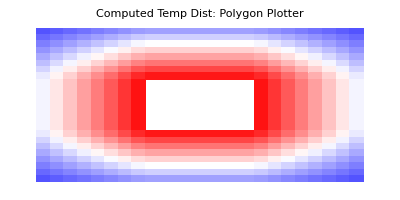

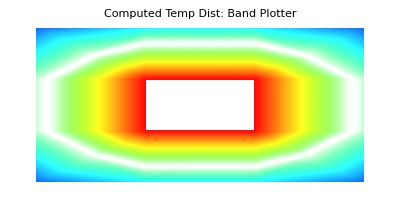

```mathematica
(*  Define FE model *)

NodeCoordinates={{0,3},{0,2},{0,1},{0,0},{2,3},{2,2},{2,1},
    {2,0},{4,3},{4,2},{4,1},{4,0},{6,3},{6,2},{6,1},{6,0}};
ElemNodes={{1,2,6,5},{2,3,7,6},{3,4,8,7},{5,6,10,9},
    {7,8,12,11},{9,10,14,13},{10,11,15,14},{11,12,16,15}};
numele=Length[ElemNodes]; numnod=Length[NodeCoordinates]; 
ElemTypes=Table["Quad4",{numele}];
ElemMaterial=Table[12,{numele}];  ElemFabrication=Table[1,{numele}];
ElemForces=Table[{0,{0,0,0,0}},{numele}];  qx=-500; qy=1500;
ElemForces[[1]]={0,{qx,0,0,qy}};ElemForces[[2]]={0,{qx,0,0,0}};
ElemForces[[3]]={0,{qx,qy,0,0}};ElemForces[[4]]={0,{0,0,0,qy}};
ElemForces[[5]]={0,{0,qy,0,0}}; ElemForces[[6]]={0,{0,0,qx,qy}};
ElemForces[[7]]={0,{0,0,qx,0}}; ElemForces[[8]]={0,{0,qy,qx,0}};
ProcessOptions={True};
PrintPoissonNodeCoordinates[NodeCoordinates,"Node Coordinate Data",{8,4}];
PrintPoissonElementNodesMatFab[ElemNodes,ElemMaterial,ElemFabrication,
       "Element Data",{9,4}]; 
PrintPoissonElementForces[ElemNodes,ElemForces,"Element Forces",{6,3}];
FreedomValues=FreedomTags=Table[0,{numnod}]; (* initialize & clear *)
FreedomValues[[6]]=FreedomValues[[7]]=FreedomValues[[10]]=
FreedomValues[[11]]=100; (* T=100 at 4 hole nodes *)
FreedomTags[[6]]=FreedomTags[[7]]=FreedomTags[[10]]=
FreedomTags[[11]]=1;     (* prescribed T at hole*)
PrintPoissonFreedomActivity[FreedomTags,FreedomValues,"DOF Activity Data",{6,3}];
elepar={9,1.5,1,12,{0.15,1,1}};
nodpar={3.5,1.5,-8,5,11,{0.7,0.2,0.9}}; typspec={}; imgsiz=400;
Plot2DMesh[NodeCoordinates,ElemTypes,ElemNodes,{},typspec,
  nodpar,elepar,{True,True,True,True,True},1/2,imgsiz,
  "Plot of FEM Mesh"];

(*  Solve problem and print results *)

{u,f}=LinearSolutionOfPoissonModel[NodeCoordinates,
      ElemTypes,ElemNodes,ElemMaterial,ElemFabrication,
      ElemForces,FreedomTags,FreedomValues,ProcessOptions];
PrintPoissonNodeTempForces[u,f,"Computed Solution",{6,4}];

(*  Contourplot temperature distribution *)

umax=Max[Abs[u]]; Nsub=8; 
ContourPlotNodeFuncOver2DMesh[NodeCoordinates,ElemNodes,
  u,umax,Nsub,1/2,imgsiz,"Computed Temp Dist: Polygon Plotter"];
ContourBandPlotNodeFuncOver2DMesh[NodeCoordinates,
 ElemNodes,u,{-umax,umax,umax/100},{True,False,False,False,
 False,False},{},1/2,imgsiz,"Computed Temp Dist: Band Plotter"];
```

Cell 12B. Two element "dam" problem, explained in Addendum B of take home
final exam.    T=100 over side 1-2. Flux q=60 Sqrt[2]  over 3-5-6, else q=0.  
The exact solution is a linear distribution of temperature depending only on x,
varying from T=+100 at x=0 to T=-100 at x=20.  *Any* mesh should reproduce this
exact solution.  Note that element 2 is a quad although it is shaped like a triangle.
Before running it, be sure the initialization cells have been compiled.

Node Coordinate Data

node | x-coor | y-coor
1 |     0.0000 |    10.0000
2 |     0.0000 |     0.0000
3 |    10.0000 |    10.0000
4 |    10.0000 |     0.0000
5 |    15.0000 |     5.0000
6 |    20.0000 |     0.0000

Element Data

elem | nodelist | conductivity | thickness
1 | {1, 2, 4, 3} |         12 |          1
2 | {3, 4, 6, 5} |         12 |          1

Element Forces

elem | nodelist | source s | flux q12 | flux q23 | flux q34 | flux q41
1 | {1, 2, 4, 3} |       0 |       0 |       0 |       0 |       0
2 | {3, 4, 6, 5} |       0 |       0 |       0 |   84.853 |   84.853

DOF Activity Data

node | DOF-tag | DOF-value
1 |       1 |     100
2 |       1 |     100
3 |       0 |       0
4 |       0 |       0
5 |       0 |       0
6 |       0 |       0

-Graphics-

Computed Solution

node | temperature | thermal-force
1 |  100.0000 |  600.0000
2 |  100.0000 |  600.0000
3 |       0 | -300.0000
4 |       0 |       0
5 | -50.0000 | -600.0000
6 | -100.0000 | -300.0000

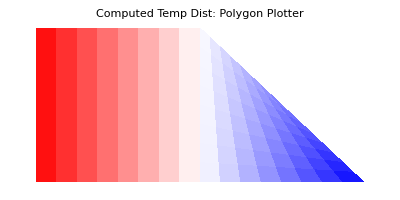

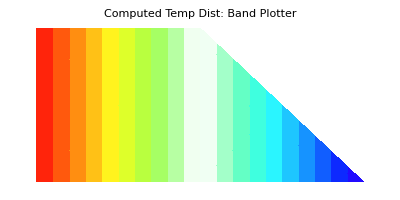

```mathematica
(*  Define FE model *)

NodeCoordinates= N[{{0,10},{0,0},{10,10},{10,0},{15,5},{20,0}}];
ElemNodes={{1,2,4,3},{3,4,6,5}}; 
PrintPoissonNodeCoordinates[NodeCoordinates,
      "Node Coordinate Data",{8,4}];
numele=Length[ElemNodes]; numnod=Length[NodeCoordinates];
ElemTypes=Table["Quad4",{numele}];  
ElemMaterial=Table[12,{numele}]; ElemFabrication=Table[1,{numele}];
ElemForces=Table[{0,{0,0,0,0}},{numele}];
ElemForces[[2]]={0,{0,0,N[60*Sqrt[2]],N[60*Sqrt[2]]}};
PrintPoissonElementNodesMatFab[ElemNodes,ElemMaterial,
       ElemFabrication,"Element Data",{9,4}];
PrintPoissonElementForces[ElemNodes,ElemForces,
      "Element Forces",{6,3}]; 
FreedomValues=FreedomTags=Table[0,{numnod}];
FreedomValues[[1]]=FreedomValues[[2]]=100; (* T @ 1,2*)
FreedomTags[[1]]=FreedomTags[[2]]=1; (* prescribed T *)
PrintPoissonFreedomActivity[FreedomTags,FreedomValues,
       "DOF Activity Data",{6,3}];    
elepar={9,1.5,1,12,{0.15,1,1}};
nodpar={3.5,1.5,-8,5,12,{0.7,0.2,0.9}}; typspec={}; imgsiz=400; 
Plot2DMesh[NodeCoordinates,ElemTypes,ElemNodes,{},typspec,
  nodpar,elepar,{False,True,True,True,True},Automatic,imgsiz,
  "Plot of FEM Mesh"];
ProcessOptions={True};
  
(*  Solve problem and print results *)

{u,f}=LinearSolutionOfPoissonModel[NodeCoordinates,
      ElemTypes,ElemNodes,ElemMaterial,ElemFabrication,
      ElemForces,FreedomTags,FreedomValues,ProcessOptions];
PrintPoissonNodeTempForces[u,f,"Computed Solution",{6,4}];

(* Contour plot temperature distribution: 2 plotters tested *)

umax=Max[Abs[u]]; Nsub=8; 
ContourPlotNodeFuncOver2DMesh[NodeCoordinates,ElemNodes,
  u,umax,Nsub,1/2,imgsiz,"Computed Temp Dist: Polygon Plotter"];
ContourBandPlotNodeFuncOver2DMesh[NodeCoordinates,
 ElemNodes,u,{-umax,umax,umax/10},{True,False,False,False,
 False,False},{},1/2,imgsiz,"Computed Temp Dist: Band Plotter"];
```

Cell 12C. Same problem as in cell above but with more elements.  Again the  exact solution should be reproduced. 
Before running it, be sure the initialization cells have been compiled.

Node Coordinate Data

node | x-coor | y-coor
1 |         0 |        10
2 |         0 |         5
3 |         0 |         0
4 |         5 |        10
5 |         5 |         5
6 |         5 |         0
7 |        10 |        10
8 |        10 |         5
9 |        10 |         0
10 |    12.5000 |     7.5000
11 |        15 |         5
12 |        15 |         0
13 |    17.5000 |     2.5000
14 |        20 |         0

Element Data

elem | nodelist | conductivity | thickness
1 | {1, 2, 5, 4} |         12 |          1
2 | {2, 3, 6, 5} |         12 |          1
3 | {4, 5, 8, 7} |         12 |          1
4 | {5, 6, 9, 8} |         12 |          1
5 | {7, 8, 11, 10} |         12 |          1
6 | {8, 9, 12, 11} |         12 |          1
7 | {11, 12, 14, 13} |         12 |          1

Element Forces

elem | nodelist | source s | flux q12 | flux q23 | flux q34 | flux q41
1 | {1, 2, 5, 4} |       0 |       0 |       0 |       0 |       0
2 | {2, 3, 6, 5} |       0 |       0 |       0 |       0 |       0
3 | {4, 5, 8, 7} |       0 |       0 |       0 |       0 |       0
4 | {5, 6, 9, 8} |       0 |       0 |       0 |       0 |       0
5 | {7, 8, 11, 10} |       0 |       0 |       0 |   84.853 |   84.853
6 | {8, 9, 12, 11} |       0 |       0 |       0 |       0 |       0
7 | {11, 12, 14, 13} |       0 |       0 |       0 |   84.853 |   84.853

DOF Activity Data

node | DOF-tag | DOF-value
1 |       1 |     100
2 |       1 |     100
3 |       1 |     100
4 |       0 |       0
5 |       0 |       0
6 |       0 |       0
7 |       0 |       0
8 |       0 |       0
9 |       0 |       0
10 |       0 |       0
11 |       0 |       0
12 |       0 |       0
13 |       0 |       0
14 |       0 |       0

Computed Solution

node | temperature | thermal-force
1 |  100.0000 |  300.0000
2 |  100.0000 |  600.0000
3 |  100.0000 |  300.0000
4 |  50.0000 |       0
5 |  50.0000 |       0
6 |  50.0000 |       0
7 |       0 | -150.0000
8 |       0 |       0
9 |       0 |       0
10 | -25.0000 | -300.0000
11 | -50.0000 | -300.0000
12 | -50.0000 |       0
13 | -75.0000 | -300.0000
14 | -100.0000 | -150.0000

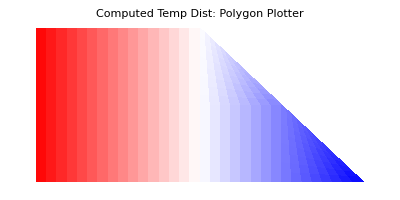

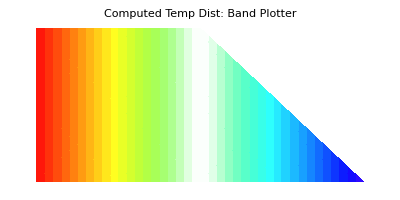

```mathematica
(*  Define FE model *)

NodeCoordinates= {{0,10},{0,5},{0,0},{5,10},{5,5},{5,0},{10,10},
  {10,5},{10,0},{12.5,7.5},{15,5},{15,0},{17.5,2.5},{20,0}};
ElemNodes={{1,2,5,4},{2,3,6,5},{4,5,8,7},{5,6,9,8},
               {7,8,11,10}, {8,9,12,11},{11,12,14,13}};  
numele=Length[ElemNodes]; numnod=Length[NodeCoordinates];
ElemTypes=Table["Quad4",{numele}];
ElemMaterial=Table[12,{numele}];  ElemFabrication=Table[1,{numele}];
ElemForces=Table[{0,{0,0,0,0}},{numele}];
ElemForces[[5]]=ElemForces[[7]]={0,{0,0,N[60*Sqrt[2]],N[60*Sqrt[2]]}};
ProcessOptions={True};
PrintPoissonNodeCoordinates[NodeCoordinates,"Node Coordinate Data",{8,4}];
PrintPoissonElementNodesMatFab[ElemNodes,ElemMaterial,ElemFabrication,
       "Element Data",{9,4}]; 
PrintPoissonElementForces[ElemNodes,ElemForces,"Element Forces",{6,3}]; 
FreedomValues=FreedomTags=Table[0,{numnod}];
FreedomValues[[1]]=FreedomValues[[2]]=FreedomValues[[3]]=100; 
FreedomTags[[1]]=FreedomTags[[2]]=FreedomTags[[3]]=1;  
PrintPoissonFreedomActivity[FreedomTags,FreedomValues,"DOF Activity Data",{6,3}];     
elepar={9,1.5,1,12,{0.15,1,1}};
nodpar={3.5,1.5,-8,5,12,{0.7,0.2,0.9}}; typspec={}; 
Plot2DMesh[NodeCoordinates,ElemTypes,ElemNodes,{},typspec,
  nodpar,elepar,{False,True,True,True,True},Automatic,"Plot of FEM Mesh"];
  
(*  Solve problem and print results *)

{u,f}=LinearSolutionOfPoissonModel[NodeCoordinates,
      ElemTypes,ElemNodes,ElemMaterial,ElemFabrication,
      ElemForces,FreedomTags,FreedomValues,ProcessOptions];
PrintPoissonNodeTempForces[u,f,"Computed Solution",{6,4}];

(*  Contourplot temperature distribution *)

umax=Max[Abs[u]]; Nsub=8; imgsiz=400;
ContourPlotNodeFuncOver2DMesh[NodeCoordinates,ElemNodes,
  u,umax,Nsub,1/2,imgsiz,"Computed Temp Dist: Polygon Plotter"];
ContourBandPlotNodeFuncOver2DMesh[NodeCoordinates,
 ElemNodes,u,{-umax,umax,umax/20},{True,False,False,False,
 False,False},{},1/2,imgsiz,"Computed Temp Dist: Band Plotter"];
```

Cell 12D. Same problem and mesh as Cell 12C, but with specified heat sink (negative source) over
 element 6.  Flux q=0 over all boundaries except 1-2-3.  The minimum temperature occurs at node 9.
 Before running it, be sure the initialization cells have been compiled.

Node Coordinate Data

node | x-coor | y-coor
1 |         0 |        10
2 |         0 |         5
3 |         0 |         0
4 |         5 |        10
5 |         5 |         5
6 |         5 |         0
7 |        10 |        10
8 |        10 |         5
9 |        10 |         0
10 |    12.5000 |     7.5000
11 |        15 |         5
12 |        15 |         0
13 |    17.5000 |     2.5000
14 |        20 |         0

Element Data

elem | nodelist | conductivity | thickness
1 | {1, 2, 5, 4} |         12 |          1
2 | {2, 3, 6, 5} |         12 |          1
3 | {4, 5, 8, 7} |         12 |          1
4 | {5, 6, 9, 8} |         12 |          1
5 | {7, 8, 11, 10} |         12 |          1
6 | {8, 9, 12, 11} |         12 |          1
7 | {11, 12, 14, 13} |         12 |          1

Element Forces

elem | nodelist | source s | flux q12 | flux q23 | flux q34 | flux q41
1 | {1, 2, 5, 4} |       0 |       0 |       0 |       0 |       0
2 | {2, 3, 6, 5} |       0 |       0 |       0 |       0 |       0
3 | {4, 5, 8, 7} |       0 |       0 |       0 |       0 |       0
4 | {5, 6, 9, 8} |    -100 |       0 |       0 |       0 |       0
5 | {7, 8, 11, 10} |       0 |       0 |       0 |       0 |       0
6 | {8, 9, 12, 11} |       0 |       0 |       0 |       0 |       0
7 | {11, 12, 14, 13} |       0 |       0 |       0 |       0 |       0

DOF Activity Data

node | DOF-tag | DOF-value
1 |       1 |     100
2 |       1 |     100
3 |       1 |     100
4 |       0 |       0
5 |       0 |       0
6 |       0 |       0
7 |       0 |       0
8 |       0 |       0
9 |       0 |       0
10 |       0 |       0
11 |       0 |       0
12 |       0 |       0
13 |       0 |       0
14 |       0 |       0

-Graphics-

Computed Solution

node | temperature | thermal-force
1 |  100.0000 |  579.1740
2 |  100.0000 |  1250.3700
3 |  100.0000 |  670.4530
4 |  18.5598 |       0
5 |  -4.0733 | -625.0000
6 | -27.0799 | -625.0000
7 | -29.0073 |       0
8 | -57.1841 | -625.0000
9 | -81.6246 | -625.0000
10 | -51.2450 |       0
11 | -63.3013 |       0
12 | -64.2995 |       0
13 | -63.9501 |       0
14 | -64.0000 |       0

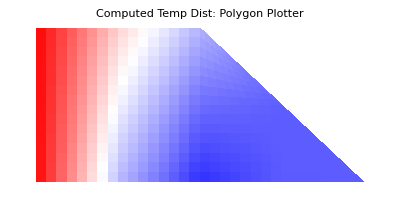

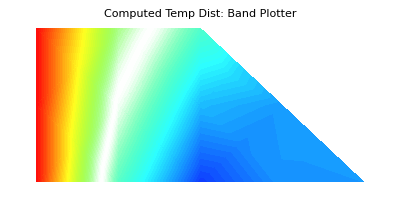

```mathematica
(*  Define FE model *)

NodeCoordinates= {{0,10},{0,5},{0,0},{5,10},{5,5},{5,0},{10,10},
  {10,5},{10,0},{12.5,7.5},{15,5},{15,0},{17.5,2.5},{20,0}};
ElemNodes={{1,2,5,4},{2,3,6,5},{4,5,8,7},{5,6,9,8},
           {7,8,11,10}, {8,9,12,11},{11,12,14,13}};
numnod=Length[NodeCoordinates]; numele=Length[ElemNodes];
ElemTypes=Table["Quad4",{numele}];
ElemMaterial=Table[12,{numele}]; ElemFabrication=Table[1,{numele}];
ElemForces=Table[{0,{0,0,0,0}},{numele}];
ElemForces[[4]]={-100,{0,0,0,0}};
PrintPoissonNodeCoordinates[NodeCoordinates,"Node Coordinate Data",{8,4}];
PrintPoissonElementNodesMatFab[ElemNodes,ElemMaterial,ElemFabrication,
       "Element Data",{9,4}]; 
PrintPoissonElementForces[ElemNodes,ElemForces,"Element Forces",{6,3}];
FreedomValues=FreedomTags=Table[0,{numnod}];
FreedomValues[[1]]=FreedomValues[[2]]=FreedomValues[[3]]=100;
FreedomTags[[1]]=FreedomTags[[2]]=FreedomTags[[3]]=1; 
ProcessOptions={True};
PrintPoissonFreedomActivity[FreedomTags,FreedomValues,"DOF Activity Data",{6,3}];      
elepar={9,1.5,1,12,{0.15,1,1}};
nodpar={3.5,1.5,-8,5,12,{0.7,0.2,0.9}}; typspec={}; imgsiz=400;
Plot2DMesh[NodeCoordinates,ElemTypes,ElemNodes,{},typspec,
  nodpar,elepar,{False,True,True,True,True},Automatic,imgsiz,
  "Plot of FEM Mesh"];
  
(*  Solve problem and print results *)

{u,f}=LinearSolutionOfPoissonModel[NodeCoordinates,
      ElemTypes,ElemNodes,ElemMaterial,ElemFabrication,
      ElemForces,FreedomTags,FreedomValues,ProcessOptions];
PrintPoissonNodeTempForces[u,f,"Computed Solution",{6,4}];

(*  ContourPlotPlot temperature distribution *)
umax=0; umax=Max[Abs[u]]; Nsub=8; 
ContourPlotNodeFuncOver2DMesh[NodeCoordinates,ElemNodes,
  u,umax,Nsub,1/2,imgsiz,"Computed Temp Dist: Polygon Plotter"];
ContourBandPlotNodeFuncOver2DMesh[NodeCoordinates,
 ElemNodes,u,{-umax,umax,umax/50},{True,False,False,False,
 False,False},{},1/2,imgsiz,
 "Computed Temp Dist: Band Plotter"];
```

Cell 13. Thermal analysis of electronic package by a very coarse mesh of 15 nodes and 8 elements. 
See mesh plot. Before running it,  be sure the initialization cells have been compiled.

Node Coordinate Data

node | x-coor | y-coor
1 |         0 |    10.1000
2 |         0 |        10
3 |         0 |     8.0000
4 |         0 |         0
5 |     3.7500 |    10.1000
6 |     3.7500 |        10
7 |     3.7500 |     8.0000
8 |     3.7500 |         0
9 |     4.6875 |    10.1000
10 |     4.6875 |        10
11 |     4.6875 |     8.0000
12 |     4.6875 |         0
13 |        25 |        10
14 |        25 |     8.0000
15 |        25 |         0

Element Data

elem | nodelist | conductivity | thickness
1 | {1, 2, 6, 5} |       150 |         1
2 | {2, 3, 7, 6} |       400 |         1
3 | {3, 4, 8, 7} |       400 |         1
4 | {5, 6, 10, 9} |       150 |         1
5 | {6, 7, 11, 10} |        40 |         1
6 | {7, 8, 12, 11} |        40 |         1
7 | {10, 11, 14, 13} |        40 |         1
8 | {11, 12, 15, 14} |        40 |         1

Element Forces

elem | nodelist | source s | flux q12 | flux q23 | flux q34 | flux q41
1 | {1, 2, 6, 5} |   16000 |       0 |       0 |       0 |      25
2 | {2, 3, 7, 6} |       0 |       0 |       0 |       0 |       0
3 | {3, 4, 8, 7} |       0 |       0 |       0 |       0 |       0
4 | {5, 6, 10, 9} |   16000 |       0 |       0 |      25 |      25
5 | {6, 7, 11, 10} |       0 |       0 |       0 |       0 |       0
6 | {7, 8, 12, 11} |       0 |       0 |       0 |       0 |       0
7 | {10, 11, 14, 13} |       0 |       0 |       0 |       0 |      10
8 | {11, 12, 15, 14} |       0 |       0 |       0 |       0 |       0

DOF Activity Data

node | DOF-tag | DOF-value
1 |       0 |       0
2 |       0 |       0
3 |       0 |       0
4 |       1 |     -20
5 |       0 |       0
6 |       0 |       0
7 |       0 |       0
8 |       1 |     -20
9 |       0 |       0
10 |       0 |       0
11 |       0 |       0
12 |       1 |     -20
13 |       0 |       0
14 |       0 |       0
15 |       1 |     -20

-Graphics-

Computed Solution

node | temperature | thermal-force
1 |  19.8336 |  1453.1200
2 |  19.2989 |  1500.0000
3 |  11.7761 |       0
4 | -20.0000 | -2914.3700
5 |  21.2289 |  1816.4100
6 |  20.7454 |  1875.0000
7 |  11.4035 |       0
8 | -20.0000 | -2942.8000
9 |  16.7131 |  362.0310
10 |  16.1048 |  272.1870
11 |   8.9843 |       0
12 | -20.0000 | -974.2430
13 | -30.7565 | -101.5630
14 | -27.0754 |       0
15 | -20.0000 | -345.7670

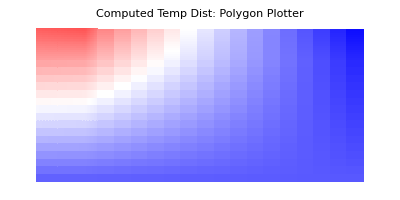

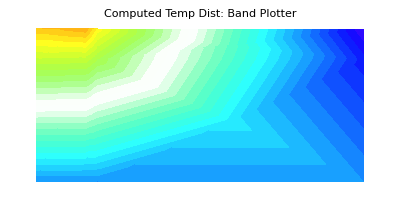

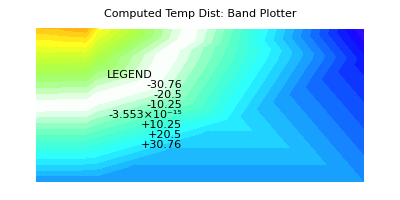

```mathematica
(*  Define FE model *)

ClearAll[a,b,c,d,f,g,e,kSi,kCu,kCer,th,Tbot,sSi,qSi,qCer];
a=25; b=10; c=5; d=3.75; e=0.1;  Tbot=-20; th=1;
kSi=150; kCu=400; kCer=40; sSi=16000; qSi=25; qCer=10;
NodeCoordinates= {{0,b+e},{0,b},{0,0.8*b},{0,0},
   {d,b+e},{d,b},{d,0.8*b},{d,0},
   {1.25*d,b+e},{1.25*d,b},{1.25*d,0.8*b},{1.25*d,0},
   {a,b},{a,0.8*b},{a,0}};
ElemNodes={{1,2,6,5},{2,3,7,6},{3,4,8,7},
           {5,6,10,9},{6,7,11,10},{7,8,12,11},
           {10,11,14,13},{11,12,15,14} }; 
numnod=Length[NodeCoordinates]; numele=Length[ElemNodes]; 
ElemTypes=Table["Quad4",{numele}];
ElemMaterial=Table[0,{numele}]; 
ElemMaterial[[1]]=ElemMaterial[[4]]=kSi;  (* silicon *)
ElemMaterial[[2]]=ElemMaterial[[3]]=kCu;  (* copper  *)
ElemMaterial[[5]]=ElemMaterial[[6]]=kCer; (* ceramic *)
ElemMaterial[[7]]=ElemMaterial[[8]]=kCer; (* ceramic *)
ElemFabrication=Table[th,{numele}];    (* unit z thickness *)
ElemForces=Table[{0,{0,0,0,0}},{numele}];
ElemForces[[1]]={sSi,  {0,0,0,qSi}};   (* silicon source & flux *)
ElemForces[[4]]={sSi,  {0,0,qSi,qSi}}; (* silicon source 7 fluxes *)
ElemForces[[7]]={0,{0,0,0,qCer}};      (* ceramic fluxes *) 
PrintPoissonNodeCoordinates[NodeCoordinates,"Node Coordinate Data",{8,4}];
PrintPoissonElementNodesMatFab[ElemNodes,ElemMaterial,ElemFabrication,
       "Element Data",{8,3}]; 
PrintPoissonElementForces[ElemNodes,ElemForces,"Element Forces",{6,3}];
FreedomValues=FreedomTags=Table[0,{numnod}];
FreedomValues[[4]]=FreedomValues[[8]]=FreedomValues[[12]]=
FreedomValues[[15]]=Tbot;  (* Chilling plate temperature *)
FreedomTags[[4]]=FreedomTags[[8]]=FreedomTags[[12]]= 
FreedomTags[[15]]=1;     (* Specified T at chilling plate *)
PrintPoissonFreedomActivity[FreedomTags,FreedomValues,"DOF Activity Data",{6,3}];
ProcessOptions={True};  aspect=4/10;    
elepar={9,1.5,1,12,{0.15,1,1}};
nodpar={3.5,1.5,-8,5,12,{0.7,0.2,0.9}}; typspec={}; imgsiz=400;
Plot2DMesh[NodeCoordinates,ElemTypes,ElemNodes,{},typspec,
  nodpar,elepar,{False,True,True,True,True},Automatic,imgsiz,
  "Electronic Package: Coarse Mesh"]; (* zoom plot to see chip better *)

(*  Solve problem and print results *)

{u,f}=LinearSolutionOfPoissonModel[NodeCoordinates,
      ElemTypes,ElemNodes,ElemMaterial,ElemFabrication,
      ElemForces,FreedomTags,FreedomValues,ProcessOptions];
PrintPoissonNodeTempForces[u,f,"Computed Solution",{6,4}];

(*  Plot temperature distribution. Last one places a legend table *)

umax=0; umax=Max[Abs[u]]; Nsub=16; 
ContourPlotNodeFuncOver2DMesh[NodeCoordinates,ElemNodes,
  u,umax,Nsub,1/2,imgsiz,"Computed Temp Dist: Polygon Plotter"];
ContourBandPlotNodeFuncOver2DMesh[NodeCoordinates,
 ElemNodes,u,{-umax,umax,umax/20},{True,False,False,False,
 False,False},{},1/2,imgsiz,"Computed Temp Dist: Band Plotter"];
ContourBandPlotNodeFuncOver2DMesh[NodeCoordinates,
 ElemNodes,u,{-umax,umax,umax/20},{True,False,False,False,
 False,False},{5,7},1/2,imgsiz,"Computed Temp Dist: Band Plotter"];
```

Place Question 5 solution script in next cell - previous one may be used as "template"

-Graphics-

Computed Solution

node | temperature | thermal-force
1 |  19.5595 |  726.5630
2 |  19.0422 |  750.0000
3 |  15.0855 |       0
4 |  11.1216 |       0
5 |   5.1737 |       0
6 |  -2.6900 |       0
7 | -10.4312 |       0
8 | -20.0000 | -1430.1700
9 |  19.5975 |  1453.1200
10 |  19.0818 |  1500.0000
11 |  15.1417 |       0
12 |  11.1366 |       0
13 |   5.1148 |       0
14 |  -2.7535 |       0
15 | -10.4683 |       0
16 | -20.0000 | -2849.3100
17 |  20.2310 |  968.7500
18 |  19.7061 |  1000.0000
19 |  15.3768 |       0
20 |  10.9906 |       0
21 |   4.8614 |       0
22 |  -2.9537 |       0
23 | -10.5788 |       0
24 | -20.0000 | -1884.6800
25 |  21.4455 |  484.3750
26 |  20.9147 |  500.0000
27 |  15.1644 |       0
28 |  10.8125 |       0
29 |   4.7103 |       0
30 |  -3.0527 |       0
31 | -10.6315 |       0
32 | -20.0000 | -514.1350
33 |  22.6933 |  240.9370
34 |  22.2366 |  244.3750
35 |  12.3197 |       0
36 |   8.5003 |       0
37 |   3.0047 |       0
38 |  -4.1312 |       0
39 | -11.1977 |       0
40 | -20.0000 | -104.6700
41 |   9.3278 | -20.3125
42 |   8.2260 |       0
43 |   5.1830 |       0
44 |   0.5915 |       0
45 |  -5.6467 |       0
46 | -11.9929 |       0
47 | -20.0000 | -239.8270
48 |  -5.5868 | -42.5000
49 |  -5.5344 |       0
50 |  -5.9185 |       0
51 |  -7.5334 |       0
52 | -10.7972 |       0
53 | -14.7175 |       0
54 | -20.0000 | -341.9280
55 | -15.3188 | -53.1250
56 | -15.1685 |       0
57 | -15.2044 |       0
58 | -15.5169 |       0
59 | -16.4608 |       0
60 | -17.8779 |       0
61 | -20.0000 | -210.3770
62 | -19.0509 | -53.1250
63 | -18.8409 |       0
64 | -18.7121 |       0
65 | -18.6818 |       0
66 | -18.8853 |       0
67 | -19.3046 |       0
68 | -20.0000 | -77.3050
69 | -20.0248 | -26.5625
70 | -19.8064 |       0
71 | -19.6498 |       0
72 | -19.5168 |       0
73 | -19.5194 |       0
74 | -19.6797 |       0
75 | -20.0000 | -20.1042

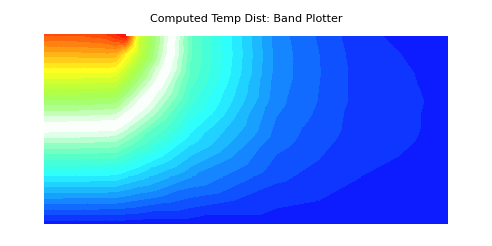

```mathematica
(*  Define FE model *)

ClearAll[a,b,c,d,f,g,e,kSi,kCu,kCer,th,Tbot,sSi,qSi,qCer];
a=25; b=10; c=5; d=3.75; e=0.1;  Tbot=-20; th=1;
kSi=150; kCu=400; kCer=40; sSi=16000; qSi=25; qCer=10;
NodeCoordinates= {{0,b+e},{0,b},{0,b-.1*b},{0,b-.2*b},{0,b-.35*b},
{0,b-.55*b},{0,b-.75*b},{0,0},{d/2,b+e},{d/2,b},{d/2,b-.1*b},{d/2,b-.2*b},
{d/2,b-.35*b},{d/2,b-.55*b},{d/2,b-.75*b},{d/2,0},{d,b+e},{d,b},{d,b-.1*b},
{d,b-.2*b},{d,b-.35*b},{d,b-.55*b},{d,b-.75*b},{d,0},{(c-d)/2+d,b+e},
{(c-d)/2+d,b},{(c-d)/2+d,b-.1*b},{(c-d)/2+d,b-.2*b},{(c-d)/2+d,b-.35*b},
{(c-d)/2+d,b-.55*b},{(c-d)/2+d,b-.75*b},{(c-d)/2+d,0},{c,b+e},{c,b},
{c,b-.1*b},{c,b-.2*b},{c,b-.35*b},{c,b-.55*b},{c,b-.75*b},{c,0},{.1*(a-d)+d,b},
{.1*(a-d)+d,b-.1*b},{.1*(a-d)+d,b-.2*b},{.1*(a-d)+d,b-.35*b},{.1*(a-d)+d,b-.55*b},
{.1*(a-d)+d,b-.75*b},{.1*(a-d)+d,0},{.25*(a-d)+d,b},{.25*(a-d)+d,b-.1*b},
{.25*(a-d)+d,b-.2*b},{.25*(a-d)+d,b-.35*b},{.25*(a-d)+d,b-.55*b},{.25*(a-d)+d,b-.75*b},
{.25*(a-d)+d,0},{.5*(a-d)+d,b},{.5*(a-d)+d,b-.1*b},{.5*(a-d)+d,b-.2*b},
{.5*(a-d)+d,b-.35*b},{.5*(a-d)+d,b-.55*b},{.5*(a-d)+d,b-.75*b},{.5*(a-d)+d,0},
{.75*(a-d)+d,b},{.75*(a-d)+d,b-.1*b},{.75*(a-d)+d,b-.2*b},{.75*(a-d)+d,b-.35*b},
{.75*(a-d)+d,b-.55*b},{.75*(a-d)+d,b-.75*b},{.75*(a-d)+d,0},{a,b},
{a,b-.1*b},{a,b-.2*b},{a,b-.35*b},{a,b-.55*b},{a,b-.75*b},{a,0}};
ElemNodes={{1,2,10,9},{2,3,11,10},{3,4,12,11},{4,5,13,12},{5,6,14,13},
{6,7,15,14},{7,8,16,15},{9,10,18,17},{10,11,19,18},{11,12,20,19},
{12,13,21,20},{13,14,22,21},{14,15,23,22},{15,16,24,23},{17,18,26,25},
{18,19,27,26},{19,20,28,27},{20,21,29,28},{21,22,30,29},{22,23,31,30},
{23,24,32,31},{25,26,34,33},{26,27,35,34},{27,28,36,35},{28,29,37,36},
{29,30,38,37},{30,31,39,38},{31,32,40,39},{34,35,42,41},{35,36,43,42},
{36,37,44,43},{37,38,45,44},{38,39,46,45},{39,40,47,46},{41,42,49,48},
{42,43,50,49},{43,44,51,50},{44,45,52,51},{45,46,53,52},{46,47,54,53},
{48,49,56,55},{49,50,57,56},{50,51,58,57},{51,52,59,58},{52,53,60,59},
{53,54,61,60},{55,56,63,62},{56,57,64,63},{57,58,65,64},{58,59,66,65},
{59,60,67,66},{60,61,68,67},{62,63,70,69},{63,64,71,70},{64,65,72,71},
{65,66,73,72},{66,67,74,73},{67,68,75,74}}; 
numnod=Length[NodeCoordinates]; numele=Length[ElemNodes]; 
ElemTypes=Table["Quad4",{numele}];
ElemMaterial=Table[0,{numele}]; 
ElemMaterial[[1]]=ElemMaterial[[8]]=ElemMaterial[[15]]=ElemMaterial[[22]]=kSi;  (* silicon *)
ElemMaterial[[2]]=ElemMaterial[[3]]=ElemMaterial[[4]]=ElemMaterial[[5]]=kCu;  (* copper  *)
ElemMaterial[[6]]=ElemMaterial[[7]]=ElemMaterial[[9]]=ElemMaterial[[10]]=kCu;  (* copper  *)
ElemMaterial[[11]]=ElemMaterial[[12]]=ElemMaterial[[13]]=ElemMaterial[[14]]=kCu;  (* copper  *)
ElemMaterial[[16]]=ElemMaterial[[17]]=ElemMaterial[[18]]=ElemMaterial[[19]]=kCu;  (* copper  *)
ElemMaterial[[20]]=ElemMaterial[[21]]=kCu;  (* copper  *)
ElemMaterial[[23]]=ElemMaterial[[24]]=ElemMaterial[[25]]=ElemMaterial[[26]]=kCer; (* ceramic *)
ElemMaterial[[27]]=ElemMaterial[[28]]=ElemMaterial[[29]]=ElemMaterial[[30]]=kCer; (* ceramic *)
ElemMaterial[[31]]=ElemMaterial[[32]]=ElemMaterial[[33]]=ElemMaterial[[34]]=kCer; (* ceramic *)
ElemMaterial[[35]]=ElemMaterial[[36]]=ElemMaterial[[37]]=ElemMaterial[[38]]=kCer; (* ceramic *)
ElemMaterial[[39]]=ElemMaterial[[40]]=ElemMaterial[[41]]=ElemMaterial[[42]]=kCer; (* ceramic *)
ElemMaterial[[43]]=ElemMaterial[[44]]=ElemMaterial[[45]]=ElemMaterial[[46]]=kCer; (* ceramic *)
ElemMaterial[[47]]=ElemMaterial[[48]]=ElemMaterial[[49]]=ElemMaterial[[50]]=kCer; (* ceramic *)
ElemMaterial[[51]]=ElemMaterial[[52]]=ElemMaterial[[53]]=ElemMaterial[[54]]=kCer; (* ceramic *)
ElemMaterial[[55]]=ElemMaterial[[56]]=ElemMaterial[[57]]=ElemMaterial[[58]]=kCer; (* ceramic *)
ElemFabrication=Table[th,{numele}];    (* unit z thickness *)
ElemForces=Table[{0,{0,0,0,0}},{numele}];
ElemForces[[1]]=ElemForces[[8]]=ElemForces[[15]]={sSi,  {0,0,0,qSi}};   (* silicon source & flux *)
ElemForces[[22]]={sSi,  {0,0,qSi,qSi}}; (* silicon source 7 fluxes *)
ElemForces[[29]]=ElemForces[[35]]=ElemForces[[41]]=ElemForces[[47]]=
ElemForces[[53]]={0,{0,0,0,qCer}};      (* ceramic fluxes *) 
(*PrintPoissonNodeCoordinates[NodeCoordinates,"Node Coordinate Data",{8,4}];
PrintPoissonElementNodesMatFab[ElemNodes,ElemMaterial,ElemFabrication,
       "Element Data",{8,3}];
PrintPoissonElementForces[ElemNodes,ElemForces,"Element Forces",{6,3}];*)
FreedomValues=FreedomTags=Table[0,{numnod}];
FreedomValues[[8]]=FreedomValues[[16]]=FreedomValues[[24]]=
FreedomValues[[32]]=FreedomValues[[40]]=FreedomValues[[47]]=
FreedomValues[[54]]=FreedomValues[[61]]=FreedomValues[[68]]=
FreedomValues[[75]]=Tbot;  (* Chilling plate temperature *)
FreedomTags[[8]]=FreedomTags[[16]]=FreedomTags[[24]]=
FreedomTags[[32]]=FreedomTags[[40]]=FreedomTags[[47]]=
FreedomTags[[54]]=FreedomTags[[61]]=FreedomTags[[68]]= 
FreedomTags[[75]]=1;     (* Specified T at chilling plate *)
(*PrintPoissonFreedomActivity[FreedomTags,FreedomValues,"DOF Activity Data",{6,3}];*)
ProcessOptions={True};  aspect=4/10;    
elepar={9,1.5,1,12,{0.15,1,1}};
nodpar={3.5,1.5,-8,5,12,{0.7,0.2,0.9}}; typspec={}; imgsiz=400;
Plot2DMesh[NodeCoordinates,ElemTypes,ElemNodes,{},typspec,
  nodpar,elepar,{False,True,True,True,True},Automatic,imgsiz,
  "Electronic Package: Fine Mesh"]; (* zoom plot to see chip better *)

(*  Solve problem and print results *)

{u,f}=LinearSolutionOfPoissonModel[NodeCoordinates,
      ElemTypes,ElemNodes,ElemMaterial,ElemFabrication,
      ElemForces,FreedomTags,FreedomValues,ProcessOptions];
PrintPoissonNodeTempForces[u,f,"Computed Solution",{6,4}];

(*  Plot temperature distribution. Last one places a legend table *)

umax=0; umax=Max[Abs[u]]; Nsub=16; 
(*ContourPlotNodeFuncOver2DMesh[NodeCoordinates,ElemNodes,
  u,umax,Nsub,1/2,imgsiz,"Computed Temp Dist: Polygon Plotter"];*)
ContourBandPlotNodeFuncOver2DMesh[NodeCoordinates,
 ElemNodes,u,{-umax,umax,umax/20},{True,False,False,False,
 False,False},{},1/2,imgsiz,"Computed Temp Dist: Band Plotter"];
```